MathPlot v1 .8.7
@Author : PhD Eng Mikołaj Bilski
@Affiliation: Institute of Applied Mechanics, Poznań University of Technology
@Release date: 08.04.2022 
@Stable on: Wolfram Mathematica v12.0.0.0

```mathematica
SetOptions[$FrontEnd,IgnoreSpellCheck->True];
settings="(*settings: modify only below this line*)";
settingsGroupCaptions="SETTINGS #";
mathPlotManipulateCaptions="MathPlot Manipulate #";
```

```mathematica
(*
Format->Option Inspector->Notebook Options->Evaluation Options;
InitializationCellEvaluation=True (mathPlot.nb);
InitializationCellWarning=False (mathPlot.nb);
GlobalInitializationCellWarning=False (Global Preferences);
*)
(*================ ADDITIONAL FUNCTIONS THAT NEED INITIALIZATION ================*)
PrintTemporary[Row[{"Initialization",ProgressIndicator[Appearance->"Percolate"]}]];
(*compute*)
compute[]:=If[computeReady,(
   computeReady=False;
   NotebookFind[SelectedNotebook[],"(*computation cell - don't make any changes unless you know exactly what you are doing*)"];
   FrontEndExecute[FrontEndToken[SelectedNotebook[],"EvaluateCells"]]
)]; computeReady=True;

(*execute*)
execute[arg_,settNum_Integer]:=If[settingsReady,(
   settingsReady=False; settingsExecutedNumber=settNum;
   NotebookFind[SelectedNotebook[],arg,All];
   FrontEndExecute[FrontEndToken[SelectedNotebook[],"EvaluateCells"]]
)]; settingsReady=True; settingsExecutedNumber=1;

(*closeAll*)
closeAll[arg_]:=(
   NotebookFind[SelectedNotebook[],arg,All];
   FrontEndExecute[FrontEndToken[SelectedNotebook[],"SelectionCloseAllGroups"]]
);

(*openExecutedSettings*)
openExecutedSettings[settingsExecutedNumber_]:=(
   NotebookFind[SelectedNotebook[],settingsGroupCaptions<>ToString[settingsExecutedNumber]<>":",All];
   FrontEndExecute[FrontEndToken[SelectedNotebook[],"SelectionOpenAllGroups"]]
);

(*clear*)
clear[]:=(
   initialLength=Length[Cells[]]-Position[Cells[],x_/;x===Cells[CellTags->"clear"][[1]]][[1,1]];
   For[i=1,i≤initialLength,i++,
      SelectionMove[SelectedNotebook[],Next,Cell];
      FrontEndExecute[FrontEndToken[SelectedNotebook[],"Clear"]];
      SelectionMove[SelectedNotebook[],Next,Cell]; SelectionMove[SelectedNotebook[],Previous,Cell]
   ]
);

(*preprocess*)
preprocess[]:=Quiet[
   Unset[plotGroups]; Clear[plotGroups];
   Unset[exportFileName]; Clear[exportFileName];
   Unset[frameLabels]; Clear[frameLabels];
   Unset[labelStyle]; Clear[labelStyle];
   Unset[aspectRatio]; Clear[aspectRatio];
   Unset[outputImageSize]; Clear[outputImageSize];
   Unset[outputImagePadding]; Clear[outputImagePadding];
   Unset[fitsXFittingRangeTableFunction]; Clear[fitsXFittingRangeTableFunction];
   Unset[fitsXSpanRangeTableFunction]; Clear[fitsXSpanRangeTableFunction];
   Unset[legendPosition]; Clear[legendPosition];
   Unset[legendDescriptionsAutomaticFitsDefaultLabel]; Clear[legendDescriptionsAutomaticFitsDefaultLabel];
   Unset[legendLayout]; Clear[legendLayout];
   Unset[legendInScaledPosition]; Clear[legendInScaledPosition];
   Unset[legendOutRelativePosition]; Clear[legendOutRelativePosition];
   Unset[legendFunction]; Clear[legendFunction];
   Unset[legendLabelStyle]; Clear[legendLabelStyle];
   Unset[legendSpacings]; Clear[legendSpacings];
   Unset[legendElementSize]; Clear[legendElementSize];
   Unset[insets]; Clear[insets];
   Unset[showPartComputingTimes]; Clear[showPartComputingTimes];
   For[z=1,z≤2,z++,
      Unset[xlsFileName[z]]; Clear[xlsFileName[z]];
      Unset[xlsLabels[z]]; Clear[xlsLabels[z]];
      Unset[xScale[z]]; Clear[xScale[z]]; 
      Unset[yScale[z]]; Clear[yScale[z]];
      Unset[plots[z]]; Clear[plots[z]];
      Unset[scatter[z]]; Clear[scatter[z]];
      Unset[splines[z]]; Clear[splines[z]];
      Unset[fits[z]]; Clear[fits[z]];
      Unset[plotRange[z]]; Clear[plotRange[z]];
      Unset[frameTicks[z]]; Clear[frameTicks[z]];
      Unset[gridLines[z]]; Clear[gridLines[z]];
      Unset[colorsListScatter[z]]; Clear[colorsListScatter[z]];
      Unset[colorsListSplines[z]]; Clear[colorsListSplines[z]];
      Unset[colorsListFits[z]]; Clear[colorsListFits[z]];
      Unset[markersTable[z]]; Clear[markersTable[z]];
      Unset[markerSize[z]]; Clear[markerSize[z]];
      Unset[splinesStyle[z]]; Clear[splinesStyle[z]];
      Unset[fitsStyle[z]]; Clear[fitsStyle[z]];
      Unset[interpolationOrder[z]]; Clear[interpolationOrder[z]];
      Unset[splinesFilling[z]]; Clear[splinesFilling[z]];
      Unset[fittingFunctions[z]]; Clear[fittingFunctions[z]];
      Unset[fitApparently[z]]; Clear[fitApparently[z]];
      Unset[fitsFilling[z]]; Clear[fitsFilling[z]];
      Unset[fitsMethod[z]]; Clear[fitsMethod[z]];
      Unset[additionalPlots[z]]; Clear[additionalPlots[z]];
      Unset[additionalPlotsRelativePosition[z]]; Clear[additionalPlotsRelativePosition[z]];
      Unset[additionalPlotsOnInsets[z]]; Clear[additionalPlotsOnInsets[z]];
      Unset[additionalGraphics[z]]; Clear[additionalGraphics[z]];
      Unset[additionalGraphicsRelativePosition[z]]; Clear[additionalGraphicsRelativePosition[z]];
      Unset[additionalGraphicsOnInsets[z]]; Clear[additionalGraphicsOnInsets[z]];
      Unset[labeledArrowsStylesAndFonts[z]]; Clear[labeledArrowsStylesAndFonts[z]];
      Unset[legendDescriptionsList[z]]; Clear[legendDescriptionsList[z]];
      Unset[legendDescriptionsSpaceForMissingPlots[z]]; Clear[legendDescriptionsSpaceForMissingPlots[z]];
      Unset[legendDescriptionsAutomaticFits[z]]; Clear[legendDescriptionsAutomaticFits[z]];
      Unset[legendAdditionalSymbols[z]]; Clear[legendAdditionalSymbols[z]]
   ]  
];

(*marker identifiers*)
markerOptions={PlotRange->{{-1.5,1.5},{-1.5,1.5}},AspectRatio->1,ImageSize->20};
blank=0; openSquare=1; openCircle=2; openUpTriangle=3; openDownTriangle=4; openDiamond=5; openLeftTriangle=6; openRightTriangle=7; openUpPentagon=8; openHorHexagon=9; openDownPentagon=10; openVerHexagon=11; openCauliflower=12; openUpPentagram=13; openDavidStar=14; openOctagonStar=15; openDownPentagram=16; openDavidStarRotated=17; openOctagonStarRotated=18; skewCross=19; straightCross=20; fillSquare=21; fillCircle=22; fillUpTriangle=23; fillDownTriangle=24; fillDiamond=25; fillLeftTriangle=26; fillRightTriangle=27; fillUpPentagon=28; fillHorHexagon=29; fillDownPentagon=30; fillVerHexagon=31; fillCauliflower=32; fillUpPentagram=33; fillDavidStar=34; fillOctagonStar=35; fillDownPentagram=36; fillDavidStarRotated=37; fillOctagonStarRotated=38; skewCrossedSquare=39; skewCrossedCircle=40; skewCrossedUpTriangle=41; skewCrossedDownTriangle=42; skewCrossedDiamond=43; skewCrossedLeftTriangle=44; skewCrossedRightTriangle=45; skewCrossedUpPentagon=46; skewCrossedHorHexagon=47; skewCrossedDownPentagon=48; skewCrossedVerHexagon=49; skewCrossedCauliflower=50; skewCrossedUpPentagram=51; skewCrossedDavidStar=52; skewCrossedOctagonStar=53; skewCrossedDownPentagram=54; skewCrossedDavidStarRotated=55; skewCrossedOctagonStarRotated=56; straightCrossedSquare=57; straightCrossedCircle=58; straightCrossedUpTriangle=59; straightCrossedDownTriangle=60; straightCrossedDiamond=61; straightCrossedLeftTriangle=62; straightCrossedRightTriangle=63; straightCrossedUpPentagon=64; straightCrossedHorHexagon=65; straightCrossedDownPentagon=66; straightCrossedVerHexagon=67; straightCrossedCauliflower=68; straightCrossedUpPentagram=69; straightCrossedDavidStar=70; straightCrossedOctagonStar=71; straightCrossedDownPentagram=72; straightCrossedDavidStarRotated=73; straightCrossedOctagonStarRotated=74;
OpenPolygon[n_, ϕ_, rOkreguOpisanego_] := {
   CapForm["Round"], JoinForm["Round"], 
   Line[Table[{rOkreguOpisanego*Cos[ϕ*Degree + i*2 π/n], rOkreguOpisanego*Sin[ϕ*Degree + i*2 π/n]}, {i, 0, n}]]
};
FillPolygon[n_, ϕ_, rOkreguOpisanego_] := {
   Polygon[Table[{rOkreguOpisanego*Cos[ϕ*Degree + i*2 π/n], rOkreguOpisanego*Sin[ϕ*Degree + i*2 π/n]}, {i, 0, n}]]
};
OpenCauliflower[probkowanie_, rOkreguOpisanego_] := {
   CapForm["Round"], JoinForm["Round"], 
   Line[Table[{rOkreguOpisanego*(Abs[Cos[25 i/probkowanie]]*0.15 + 0.6)*Cos[i*2 π/probkowanie], rOkreguOpisanego*(Abs[Cos[25 i/probkowanie]]*0.15 + 0.6)*Sin[i*2 π/probkowanie]}, {i, 0, probkowanie}]]
};
FillCauliflower[probkowanie_, rOkreguOpisanego_] := {
   Polygon[Table[{rOkreguOpisanego*(Abs[Cos[25 i/probkowanie]]*0.15 + 0.6)*Cos[i*2 π/probkowanie], rOkreguOpisanego*(Abs[Cos[25 i/probkowanie]]*0.15 + 0.6)*Sin[i*2 π/probkowanie]}, {i, 0, probkowanie}]]
};
StylizedOpenPolygon[list_]:={
   CapForm["Round"], JoinForm["Round"],
   Line[list]
};
graphs = {
   {Thickness[0.1*sizeMod], OpenPolygon[4, 45, 0.95*sizeMod]},
   {Thickness[0.1*sizeMod], Circle[{0, 0}, Sqrt[2]/2*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 90, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 270, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[4, 0, 0.8*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 180, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 0, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 18, 0.78*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 0, 0.73*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 198, 0.78*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 90, 0.73*sizeMod]},
   {Thickness[0.07*sizeMod], OpenCauliflower[50, 0.72*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,0.2927},{0,0.9388},{0.2145,0.2927},{0.8829,0.2927},{0.3469,-0.1097},{0.5534,-0.7611},{0,-0.3692},{-0.5534,-0.7611},{-0.3469,-0.1097},{-0.8829,0.2927},{-0.2145,0.2927}}]},
   {Thickness[0.07*sizeMod], (ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}])},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,-0.2927},{0,-0.9388},{0.2145,-0.2927},{0.8829,-0.2927},{0.3469,0.1097},{0.5534,0.7611},{0,0.3692},{-0.5534,0.7611},{-0.3469,0.1097},{-0.8829,-0.2927},{-0.2145,-0.2927}}]},
   {Thickness[0.07*sizeMod], Rotate[(ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}]),30Degree]},
   {Thickness[0.07*sizeMod], Rotate[StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}],45/2Degree]},
   {Thickness[0.1*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[4, 45, 0.95*sizeMod]},
   {Thickness[0.1*sizeMod], Disk[{0, 0}, Sqrt[2]/2*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[3, 90, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[3, 270, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[4, 0, 0.8*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[3, 180, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[3, 0, 0.85*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[5, 18, 0.78*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[6, 0, 0.73*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[5, 198, 0.78*sizeMod]},
   {Thickness[0.1*sizeMod], FillPolygon[6, 90, 0.73*sizeMod]},
   {Thickness[0.1*sizeMod], FillCauliflower[50, 0.72*sizeMod]},
   {Thickness[0.1*sizeMod], Polygon[0.8*sizeMod*{{-0.8829,0.2927},{-0.2145,0.2927},{0,0.9388},{0.2145,0.2927},{0.8829,0.2927},{0.3469,-0.1097},{0.5534,-0.7611},{0,-0.3692},{-0.5534,-0.7611},{-0.3469,-0.1097}}]},
   {Thickness[0.1*sizeMod], (ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;Polygon[0.8*sizeMod*{{0,ROpis},{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2}}])},
   {Thickness[0.1*sizeMod], Polygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}]},
   {Thickness[0.1*sizeMod], Polygon[0.8*sizeMod*{{-0.8829,-0.2927},{-0.2145,-0.2927},{0,-0.9388},{0.2145,-0.2927},{0.8829,-0.2927},{0.3469,0.1097},{0.5534,0.7611},{0,0.3692},{-0.5534,0.7611},{-0.3469,0.1097}}]},
   {Thickness[0.1*sizeMod], Rotate[(ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;Polygon[0.8*sizeMod*{{0,ROpis},{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2}}]),30Degree]},
   {Thickness[0.1*sizeMod], Rotate[Polygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}],45/2Degree]},
   {Thickness[0.1*sizeMod], OpenPolygon[4, 45, 0.95*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], Circle[{0, 0}, Sqrt[2]/2*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 90, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 270, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[4, 0, 0.8*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 180, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 0, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 18, 0.78*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 0, 0.73*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 198, 0.78*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 90, 0.73*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], OpenCauliflower[50, 0.72*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,0.2927},{0,0.9388},{0.2145,0.2927},{0.8829,0.2927},{0.3469,-0.1097},{0.5534,-0.7611},{0,-0.3692},{-0.5534,-0.7611},{-0.3469,-0.1097},{-0.8829,0.2927},{-0.2145,0.2927}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], (ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}]), Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,-0.2927},{0,-0.9388},{0.2145,-0.2927},{0.8829,-0.2927},{0.3469,0.1097},{0.5534,0.7611},{0,0.3692},{-0.5534,0.7611},{-0.3469,0.1097},{-0.8829,-0.2927},{-0.2145,-0.2927}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], Rotate[(ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}]),30Degree], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.07*sizeMod], Rotate[StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}],45/2Degree], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{-1, -1}, {1, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 1}, {1, -1}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[4, 45, 0.95*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], Circle[{0, 0}, Sqrt[2]/2*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 90, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 270, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[4, 0, 0.8*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 180, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[3, 0, 0.85*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 18, 0.78*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 0, 0.73*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[5, 198, 0.78*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.1*sizeMod], OpenPolygon[6, 90, 0.73*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], OpenCauliflower[50, 0.72*sizeMod], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,0.2927},{0,0.9388},{0.2145,0.2927},{0.8829,0.2927},{0.3469,-0.1097},{0.5534,-0.7611},{0,-0.3692},{-0.5534,-0.7611},{-0.3469,-0.1097},{-0.8829,0.2927},{-0.2145,0.2927}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], (ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}]), Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], StylizedOpenPolygon[0.8*sizeMod*{{-0.2145,-0.2927},{0,-0.9388},{0.2145,-0.2927},{0.8829,-0.2927},{0.3469,0.1097},{0.5534,0.7611},{0,0.3692},{-0.5534,0.7611},{-0.3469,0.1097},{-0.8829,-0.2927},{-0.2145,-0.2927}}], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], Rotate[(ROpis=0.9;aDuzegoTrojkata=3ROpis/Sqrt[3];hMalyTrojkat=aDuzegoTrojkata/3*Sqrt[3]/2;StylizedOpenPolygon[0.8*sizeMod*{{aDuzegoTrojkata/6,ROpis/2},{aDuzegoTrojkata/2,ROpis/2},{aDuzegoTrojkata/3,0},{aDuzegoTrojkata/2,-ROpis/2},{aDuzegoTrojkata/6,-ROpis/2},{0,-ROpis},{-aDuzegoTrojkata/6,-ROpis/2},{-aDuzegoTrojkata/2,-ROpis/2},{-aDuzegoTrojkata/3,0},{-aDuzegoTrojkata/2,ROpis/2},{-aDuzegoTrojkata/6,ROpis/2},{0,ROpis},{aDuzegoTrojkata/6,ROpis/2}}]),30Degree], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]},
   {Thickness[0.07*sizeMod], Rotate[StylizedOpenPolygon[0.8*sizeMod*{{0,0.5},{0.3642,0.8771},{0.3642,0.3642},{0.8771,0.3642},{0.5,0},{0.8771,-0.3642},{0.3642,-0.3642},{0.3642,-0.8771},{0,-0.5},{-0.3642,-0.8771},{-0.3642,-0.3642},{-0.8771,-0.3642},{-0.5,0},{-0.8771,0.3642},{-0.3642,0.3642},{-0.3642,0.8771},{0,0.5}}],45/2Degree], Thickness[0.05*sizeMod], Line[Sqrt[2]/2*{{0, -1}, {0, 1}}*sizeMod], Line[Sqrt[2]/2*{{-1, 0}, {1, 0}}*sizeMod]}
   };
MathPlot::exceededLimitOfMarkers = "Number of defined markers (`1`) has been exceeded. Looped symbols will be used.";
marker[z_Integer,i_Integer, size_] := Graphics[If[markersTable[z][[i]]>0,Prepend[graphs[[markersTable[z][[i]]]]/.sizeMod->size,colorsListScatter[z][[i]]],{Text[""]}],markerOptions];
	
(*linearDependence*) 
linearDependence[z_Integer,i_Integer,firstValue_,lastValue_,numberOfPlots___]:=
 (finalNumberOfPlots=If[numberOfPlots===Null,Length[plotsData[z]],numberOfPlots];
  firstValue-If[finalNumberOfPlots>1,
  (i-1)/(finalNumberOfPlots-1)*(firstValue-lastValue),
  0]
 );
	
(*useColorScheme*) 
useColorScheme[z_Integer,colorSchemeName_,setSize_]:=
 (If[setSize===All || setSize===Automatic,
  setSizeFinal=Length[plotsData[z]],setSizeFinal=setSize];
  Quiet[Thread@{ColorData[colorSchemeName]/@Range[0,1,1/(setSizeFinal-1)]}[[1]]]
 );

(*plotFunExpression*)
plotFunExpression[z_Integer] := If[xScale[z] === Lin, 
   If[yScale[z] === Lin, Plot, LogPlot], 
   If[yScale[z] === Lin, LogLinearPlot, LogLogPlot]
];

(*linePlotSymbol*)
linePlotSymbol[styleOpts__]:={Directive[styleOpts],Line[{{-1.5,0},{1.5,0}}]};
 
(*labeledArrow*)
labeledArrow[z_Integer, coords_, label_] := If[Length[coords] == 2 || Length[coords] == 3, 
   (If[Length[coords] == 2, 
    finalCoords = coords, 
    finalCoords = {Scaled[coords[[3, 1]] + coords[[2]]*{Cos[coords[[1]]], Sin[coords[[1]]]}], coords[[3]]}]; 
    Join[labeledArrowsStylesAndFonts[z][[1]],{Arrow[finalCoords],Text[Style[label, labeledArrowsStylesAndFonts[z][[2]]], finalCoords[[1]], If[If[Length[finalCoords[[1]]] == 1, finalCoords[[1, 1, 2]], finalCoords[[1, 2]]] < If[Length[finalCoords[[2]]] == 1, finalCoords[[2, 1, 2]], finalCoords[[2, 2]]], {0, 1}, {0, -1}]]}]
   )
];
 
(*plotInset*)
plotInset[z_Integer,plotInsetRange_,plotInsetPosition_,plotInsetSize_,plotInsetFrameStyle_,mainPlotRegionFrameDashing_,plotInsetFrameTicks_,plotInsetGridLines_]:=
   {z,plotInsetRange,plotInsetPosition,plotInsetSize,plotInsetFrameStyle,mainPlotRegionFrameDashing,plotInsetFrameTicks,plotInsetGridLines};

(*getLegendSplinesDirectives*)
getLegendSplinesDirectives[styles_,i_Integer]:=Table[Which[
   StringContainsQ[ToString[styles[i][[j]]],"Dashing"],
      If[StringContainsQ[ToString[styles[i][[j]]],"Small"],
         If[Length[styles[i][[j,1]]]==4,
            (*DotDashed*)Dashing[{0,0.15,0.15,0.15}],
            If[StringContainsQ[ToString[styles[i][[j]]],"0"],
               (*Dotted*)Dashing[{0,0.1}],
               (*Dashed*)Dashing[{0.2,0.2}]
            ]
         ],
         Dashing[styles[i][[j]][[1]]*10]
      ],
   StringContainsQ[ToString[styles[i][[j]]],"Thickness"],
      Thickness[styles[i][[j]][[1]]*20*legendElementSize],
   !(styles[i][[j]]===Null),
      styles[i][[j]]
   ],{j,Length[styles[i]]}]; 
 
(*fitsDetails*)
fitsDetails[z_Integer]:=If[ValueQ[fits[z]] && Length[fits[z]]>0,(
   For[i=Length[fitsDetailsIDs[z]],i<Length[fits[z]],i++,AppendTo[fitsDetailsIDs[z],Graphics[Line[{{-1,0},{1,0}}],PlotRange->{{-1,1},{-0.2,0.2}},ImageSize->50]]];
   TableForm[
   Table[{
      fitsDetailsIDs[z][[i]],
      fitsExpressions[z][[i]]["RSquared"],
      fitsExpressions[z][[i]]["AdjustedRSquared"],
      fittingFunctions[z][x][[i,1]],
      TableForm[fitsExpressions[z][[i]]["BestFitParameters"]],
      (errors=fitsExpressions[z][[i]]["ParameterErrors"];For[j=1,j≤Length[errors],j++,errors[[j]]="Δ"fittingFunctions[z][x][[i,2,j]]->errors[[j]]];TableForm[errors]),
      fitsExpressions[z][[i]]["BestFit"],
      If[fitApparently[z][[i]]&&(xScale[z]===Log||yScale[z]===Log),fitPlotsData[z][[i]],Graphics[Line[{{-1,0},{1,0}}],PlotRange->{{-1,1},{-0.2,0.2}},ImageSize->50]]
   },{i,Length[fits[z]]}],
   TableHeadings->{
      Table[Graphics[{Directive[Join[
         getLegendSplinesDirectives[fitsStyle[z],fits[z][[i]]],{colorsListFits[z][[fits[z][[i]]]]}]],
         Line[{{markerOptions[[1,2,1,1]],0},{markerOptions[[1,2,1,2]],0}}],Dashing[None]
      },markerOptions],{i,Length[fits[z]]}],
      {"ID in legend","R-Squared","Adj. R-Squared","Model","Coefficients","Standard Errors","Best Fit","Apparent Fit form"}
   },TableSpacing->{5,4}
   ]),
   Print[Style["No fits found for '"<>ToString[z]<>"' parameter.",Red]]
];

(*MathPlot Manipulate preprocessing functions*)
pointer[u_]:=ListPlot[{u},PlotMarkers->{Graphics[{Red,Thickness[0.25],Line[{{-1,-1},{1,1}}],Line[{{-1,1},{1,-1}}]}],0.07}];
rasteredCoords[u_,uRange_]:=rasteredLeftBotCorner+(u-uRange[[1]])/{uRange[[2,1]]-uRange[[1,1]],uRange[[2,2]]-uRange[[1,2]]}*{rasteredRightTopCorner[[1]]-rasteredLeftBotCorner[[1]],rasteredRightTopCorner[[2]]-rasteredLeftBotCorner[[2]]};
scaleDepLog[ifArg_,arg_]:=If[ifArg===Lin,arg,Log[arg]];
scaleDepE[ifArg_,arg_]:=If[ifArg===Lin,arg,E^arg];
layers[z_Integer,zActive_Integer,mode_,pointCoords_]:=If[mode,
   ControlActive[If[z==zActive,{passePartOut[z],pointer[pointCoords]},{passePartOut[z]}],If[z==zActive,Append[warstwy[z],pointer[pointCoords]],warstwy[z]]],               
   If[z==zActive,Append[warstwy[z],pointer[pointCoords]],warstwy[z]]
];
scaleFunction[scaleArgument_,shift_,mod_]:=((scaleArgument−1/4)*mod)^3+shift;
scaleRange[z_Integer,actualScalePercents_,pointCoords_,plotRange_]:=(
   xDefaultRange=(scaleDepLog[xScale[z],plotRange[[1,2]]]-scaleDepLog[xScale[z],plotRange[[1,1]]]); 
   yDefaultRange=(scaleDepLog[yScale[z],plotRange[[2,2]]]-scaleDepLog[yScale[z],plotRange[[2,1]]]);
   left=(scaleDepLog[xScale[z],pointCoords[[1]]]-scaleDepLog[xScale[z],plotRange[[1,1]]])/xDefaultRange; right=1-left;
   bottom=(scaleDepLog[yScale[z],pointCoords[[2]]]-scaleDepLog[yScale[z],plotRange[[2,1]]])/yDefaultRange; top=1-bottom;
   xMod=xDefaultRange/actualScalePercents[[1]];
   left*=xMod; right*=xMod;
   yMod=yDefaultRange/actualScalePercents[[2]];
   bottom*=yMod; top*=yMod;
   {scaleDepLog[xScale[z],If[actualScalePercents[[1]]≥1,scaleDepE[xScale[z],{scaleDepLog[xScale[z],pointCoords[[1]]]-left,scaleDepLog[xScale[z],pointCoords[[1]]]+right}],scaleDepE[xScale[z],{scaleDepLog[xScale[z],pointCoords[[1]]]-xMod/2,scaleDepLog[xScale[z],pointCoords[[1]]]+xMod/2}]]],
    scaleDepLog[yScale[z],If[actualScalePercents[[2]]≥1,scaleDepE[yScale[z],{scaleDepLog[yScale[z],pointCoords[[2]]]-bottom,scaleDepLog[yScale[z],pointCoords[[2]]]+top}],scaleDepE[yScale[z],{scaleDepLog[yScale[z],pointCoords[[2]]]-yMod/2,scaleDepLog[yScale[z],pointCoords[[2]]]+yMod/2}]]]
   }
);
getRealFromScaled[scale_,scaledCoord_,rangeInOneDimension_]:=scaleDepE[scale,rangeInOneDimension[[1]]+scaledCoord*(rangeInOneDimension[[2]]-rangeInOneDimension[[1]])];
MathPlot::plotUninitialized="Plot has not been initialized yet.";

If[!ValueQ[initMathPlotUsages] || initMathPlotUsages,initMathPlotUsages=False;
(*usages*)
MathPlot::exampleCopied = "Example '`1`' of function '`2`' has been copied to the clipboard.";
MathPlot::exampleNotFound = "Could not find example '`1`' of function '`2`'.";
SetAttributes[symFun,HoldAll]; SetAttributes[copyExample,HoldAll];
symFun[fun_]:=SymbolName[Unevaluated@fun];
symLett[lett_]:=SymbolName[Unevaluated@lett];
copyExample[function_,exampleLetter_]:=(
   textCopied=example[symFun[function],symLett[exampleLetter]];
   If[!(StringStartsQ[ToString[textCopied],"example"]),
      CopyToClipboard[textCopied];
      Message[MathPlot::exampleCopied,symLett[exampleLetter],symFun[function]],
      Message[MathPlot::exampleNotFound,symLett[exampleLetter],symFun[function]]
   ]
);
addUsage[fun_,text_String,examples___]:={
   fun::usage=StringTemplate[text][examples];
   For[i=1,i≤Length[{examples}],i++,
      example[symFun[fun],symLett[Symbol[Alphabet[][[i]]]]]={examples}[[i]]
   ]
};


addUsage[plotGroups,"Number of plot groups (1 or 2) using different axes (the same X and different Y or different both X and Y [see 'plotRange' and 'frameLabels']). Almost all other parameters have a value of 'z' in square brackets [], which indicates the group of graphs it concerns (1 or 2). In the case of not explicitly specified parameters for the group 'z=2', in most cases MathPlot will take the same value as for 'z=1'."];
addUsage[xlsFileName,"Excel file(s) to load. Examples:\n(a) `1`\n(b) `2`","\"fileName.xlsx\"","{\"fileName1.xlsx\",\"fileName2.xlsx\"}"];
addUsage[exportFileName,"Output (exported) file. Examples:\n(a) `1` (no output file)\n(b) `2`\n(c) `3`","None","\"fileName.pdf\"","{\"fileName.png\",ImageResolution->500}"];
addUsage[Skew,"Direction right-down for use in 'plots'."];
addUsage[xlsLabels,"Labels of X/Y/dY columns (respectively) in Excel sheets that should be imported. 'cmpFun' can take values such as StringStartsQ, StringEndsQ, StringContainsQ, Equal. Can take multiple packs when more than 1 'xlsFileName' is specified. Examples:\n(a) `1` - without error bars\n(b) `2` - with error bars\n(c) `3` - with (file1) and without (file2) error bars","{{\"xLabel\",cmpFun},{\"yLabel\",cmpFun}}","{{\"xLabel\",cmpFun},{\"yLabel\",cmpFun},{\"dyLabel\",cmpFun}}","{{{\"xLabelInFile1\",cmpFun},{\"yLabelInFile1\",cmpFun},{\"dyLabelInFile1\",cmpFun}},{{\"xLabelInFile2\",cmpFun},{\"yLabelInFile2\",cmpFun}}}"];
addUsage[xScale,"Scale of X axis, can take values: Lin/Log."];
addUsage[yScale,"Scale of Y axis, can take values: Lin/Log."];
addUsage[Lin,"Linear scale used by 'xScale' and/or 'yScale'."];
addUsage[plots,"Indexes (or names) of sheets of loaded xlsFile(s) with indexes of (found) Y columns (identified by 'xlsLabels') that should be imported. Can take multiple values and any index can be repeated, examples:\n(a) `1`\n(b) using Riffle[] & Join[]: `2` - sheets from 1 to 7, taking All occurrences of xlsLabels(Y)\n(c) `3`\n(d) `4` - example specifies the identifier (text) of cell in specified sheet pointing at the begining of data to import (i.e. top-left corner of labels). 'cmpFun' can take values such as StringStartsQ, StringEndsQ, StringContainsQ, Equal and 'relativeCornerDataCellDirection' can take values such as After (labels start on the right of the cell specified), Below or Skew (labels start on the bottom-right). Above examples are transformed into {{nameOfSheet,None},{ind1,ind2,...},...} by default, which means that mathPlot will search for first non-empty cell in specified sheet and treat it as the begining of the data region\n(e) Cautions: 1) When indexes are not in order, it should be noted that they are related with legend descriptions specified MANUALLY (when Automatic legends are used, procedures will adjust everything)","{indexOf1stSheet, {ind1, ind2, ...}, \"nameOf2ndSheet\", All, ...}","Join[Riffle[Table[i,{i,1,7}],{All}],{All}]","{{indexOf1stSheetInFile1, {ind1, ind2, ...}, \"nameOf2ndSheetInFile1\", All, ...},{indexOf1stSheetInFile2, {ind1, ind2, ...}, indexOf2ndSheetInFile2, All, ...}}","{{indexOrNameOfSheet,{\"text\",cmpFun,relativeCornerDataCellDirection}}, {ind1, ind2, ...}, ...}"];
addUsage[scatter,"Indexes of plots (whose order is specified in 'plots') that should be drawn as scatter (points) plot. The order of occurrence of indexes in this variable is irrelevant. Examples:\n(a) `1`\n(b) `2`\n(c) `3`","All","None","{i1,i2,...}"];
addUsage[splines,"Indexes of plots (whose order is specified in 'plots') that should connected with splines. The order of occurrence of indexes in this variable is irrelevant. Examples:\n(a) `1`\n(b) `2`\n(c) `3`","All","None","{i1,i2,...}"];
addUsage[fits,"Indexes of plots (whose order is specified in 'plots') for which fits should be drawn. The order of occurrence of indexes in this variable is connected with 'fittingFunctions'. Examples:\n(a) `1`\n(b) `2`\n(c) `3`","All","None","{i1,i2,...}"];
addUsage[plotRange,"Range of plot. In the case of plotGroups=2, if plotRange[2]=Automatic/Full or {Automatic/Full,{y0,y1}} then the X range[2] is taken from [1] plot group. Examples:\n(a) `1`\n(b) `2`\n(c) `3`\n(d) `4`\n(e) `5`\n(f) `6`","Automatic","Full","All","{{xMin,xMax},{yMin,yMax}}","{Automatic/Full,{yMin,yMax}}","{{xMin,xMax},Automatic/Full}"];
addUsage[frameLabels,"Text of frame labels. Examples:\n(a) `1` - plotGroups=1: left and bottom labels; plotGroups=2: left[1], right[2], bottom[1] labels, and the top[2] label will be created if plotRange[2]!=Automatic/Full (or if plotRange[2][[1]]!=Automatic/Full). Labels will be created using 'xlsLabels'\n(b) `2` - manually specified bottom and left label, respectively (mainly for plotGroups=1)\n(c) `3` - manually specified bottom, left[1] and right[2] label, respectively (mainly for plotGroups=2)\n(d) `4` - manually specified labels for each frame side","Automatic","{\"xLabel\",\"yLabel\"}","{\"x\",\"yLeft\",\"yRight\"}","{{left,right},{bot,top}}"];
addUsage[labelStyle,"Style of frame labels. Examples:\n(a) `1`","Directive[18,FontFamily→\"Cambria\"]"];
addUsage[aspectRatio,"Ratio of height to width for a plot. Examples:\n(a) `1`\n(b) `2` (typical value)\n(c) `3` (vertical plot)\n(d) `4` (horizontal plot)","Automatic","3/5","2","0.5"];
addUsage[frameTicks,"Settings of frame ticks [Help: FrameTicks]. GridLines will adapt to ticks (priority: left & bottom). Examples:\n(a) `1` - left & bottom\n(b) `2` - left & right & bottom & top & dense GridLines\n(c) `3` -  (...)Ticks can take values: Automatic/All/None/{value1,value2,...}/{{value1,label1},{v2,l2},{v3,l3},...}. Note that left & bottom (automatic) gridlines will have 'darkcyan' color, and right & top - 'magenta' color (as in the case of plotGroups=2). Caution: note that frameTicks have the [z] (plotGroup) parameter - when plotGroups=2 is used then ticks/gridlines can overlap\n(d) `4` - left[Automatic] & bottom[rotated dates]","Automatic","All","{{leftTicks,rightTicks},{bottomTicks,topTicks}}","{{Automatic,None},{Table[{i,Rotate[DateString[DateObject[{2020,1,0+i}],{\"Year\",\"/\",\"Month\",\"/\",\"Day\"}],-Pi/3]},{i,1,10,2}],None}}"];
addUsage[gridLines,"Settings of grid lines [Help: GridLines]. Examples:\n(a) `1` - GridLines will adapt to frameTicks specified above\n(b) `2`\n(c) `3`","Automatic","None","{listOfXGridLines,listOfYGridLines}"];
addUsage[outputImageSize,"The size of the bounding box of the plot image. Examples:\n(a) `1` - specified width of the plot frame (height is adjusted by 'aspectRatio')\n(b) `2` - specified width and height of the full output image (width/height of the plot still is adjusted by 'aspectRatio')\n(c) Caution: when legendPosition=Out is used, the size of the image will be modified in order to include the 'external' legend","500","{width,height}"];
addUsage[outputImagePadding,"The size of the padding around the plot frame. Too small padding can lead to: (1) clipping of the frame labels, (2) with plotGroups=2 the positioning of individual charts can move around (when it is too large, positioning is never a problem - but then there is a lot of white space around). It is recommended to use the default setting (example (a)), but when e.g. exceptionally large tick labels are used (large numbers or fonts) the default settings may be insufficient. Examples:\n(a) `1` - the default (recommended) settings\n(b) `2` - include only the plot frame (without even the ticks or labels of the frame)","{{85,75},{50,50}}","{{0,0},{0,0}}"];
addUsage[colorsListScatter,"List of colors used for scatter plots. Length of list must be equal to the length specified by 'plots' (not 'scatter'/'splines'/'fits'). Examples:\n(a) `1`\n(b) `2` - specify color scheme which should be used [Help: ColorSchemes]. 'listLength' can take values: Automatic/All (different colors for all plots of 'z' plotGroup [1 or 2]) or any number (then Join[] function can be used to create list of colors for all plots)\n(c) `3` - colors for 10 plots in total, using two different schemes","{color1,color2,color3,...}","useColorScheme[z,{\"Rainbow\",\"Reverse\"},listLength]","Join[useColorScheme[z,...,5],useColorScheme[z,...,5]]"];
addUsage[colorsListSplines,"List of colors used for splines. Length of list must be equal to the length specified by 'plots' (not 'scatter'/'splines'/'fits'). Examples:\n(a) `1`\n(b) `2` - specify color scheme which should be used [Help: ColorSchemes]. 'listLength' can take values: Automatic/All (different colors for all plots of 'z' plotGroup [1 or 2]) or any number (then Join[] function can be used to create list of colors for all plots)\n(c) `3` - colors for 10 plots in total, using two different schemes","{color1,color2,color3,...}","useColorScheme[z,{\"Rainbow\",\"Reverse\"},listLength]","Join[useColorScheme[z,...,5],useColorScheme[z,...,5]]"];
addUsage[colorsListFits,"List of colors used for fits. Length of list must be equal to the length specified by 'plots' (not 'scatter'/'splines'/'fits'). Examples:\n(a) `1`\n(b) `2` - specify color scheme which should be used [Help: ColorSchemes]. 'listLength' can take values: Automatic/All (different colors for all plots of 'z' plotGroup [1 or 2]) or any number (then Join[] function can be used to create list of colors for all plots)\n(c) `3` - colors for 10 plots in total, using two different schemes","{color1,color2,color3,...}","useColorScheme[z,{\"Rainbow\",\"Reverse\"},listLength]","Join[useColorScheme[z,...,5],useColorScheme[z,...,5]]"];
addUsage[markersTable,"Markers which should be used in order specified in 'plots' (i.e. BEFORE any exclusion by an incomplete 'scatter' set). Examples:\n(a) `1` - all implemented markers will be used in automatic order\n(b) `2` - only first 5 implemented markers will be used in the looped sequence\n(c) `3` - 3 specified symbols will be used in looped sequence\n(d) `4` - three groups of corresponding symbols (but skew/straight crossed) starting with 'circle'\n(e) List of all implemented symbol's indentifiers (they all are only integer numbers): blank, openSquare, openCircle, openUpTriangle, openDownTriangle, openDiamond, openLeftTriangle, openRightTriangle, openUpPentagon, openHorHexagon, openDownPentagon, openVerHexagon, openCauliflower, openUpPentagram, openDavidStar, openOctagonStar, openDownPentagram, openDavidStarRotated, openOctagonStarRotated, skewCross, straightCross, fillSquare, fillCircle, fillUpTriangle, fillDownTriangle, fillDiamond, fillLeftTriangle, fillRightTriangle, fillUpPentagon, fillHorHexagon, fillDownPentagon, fillVerHexagon, fillCauliflower, fillUpPentagram, fillDavidStar, fillOctagonStar, fillDownPentagram, fillDavidStarRotated, fillOctagonStarRotated, skewCrossedSquare, skewCrossedCircle, skewCrossedUpTriangle, skewCrossedDownTriangle, skewCrossedDiamond, skewCrossedLeftTriangle, skewCrossedRightTriangle, skewCrossedUpPentagon, skewCrossedHorHexagon, skewCrossedDownPentagon, skewCrossedVerHexagon, skewCrossedCauliflower, skewCrossedUpPentagram, skewCrossedDavidStar, skewCrossedOctagonStar, skewCrossedDownPentagram, skewCrossedDavidStarRotated, skewCrossedOctagonStarRotated, straightCrossedSquare, straightCrossedCircle, straightCrossedUpTriangle, straightCrossedDownTriangle, straightCrossedDiamond, straightCrossedLeftTriangle, straightCrossedRightTriangle, straightCrossedUpPentagon, straightCrossedHorHexagon, straightCrossedDownPentagon, straightCrossedVerHexagon, straightCrossedCauliflower, straightCrossedUpPentagram, straightCrossedDavidStar, straightCrossedOctagonStar, straightCrossedDownPentagram, straightCrossedDavidStarRotated, straightCrossedOctagonStarRotated","Automatic","5","{openSquare,openLeftTriangle,skewCross}","Join[Table[openCircle+i,{i,0,8}],Table[skewCrossedCircle+i,{i,0,8}],Table[straightCrossedCircle+i,{i,0,8}]]"];
addUsage[linearDependence,"Function dedicated for markers/lines size settings. Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1` - linearly decreasing size from 1 to 0.5 in number of steps equal to plots number\n(b) `2` - linearly decreasing size from 1 to 0.5 in 10 steps","linearDependence[z,i,1,0.5]","linearDependence[z,i,1,0.5,10]"];
addUsage[markerSize,"Function defining size of markers. 'i' refers to 'plots'. Can be any function of 'i' but in most cases the use of 'linearDependence' function is advisable. Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1` - linearly decreasing size from 1 to 0.5 in number of steps equal to plots number\n(b) `2` - linearly decreasing size from 1 to 0.5 in 10 steps","linearDependence[z,i,1,0.5]","linearDependence[z,i,1,0.5,10]"];
addUsage[splinesStyle,"Style of splines. 'i' refers to 'plots'. Can be any list of functions of 'i' but in most cases the use of 'linearDependence' function is advisable. Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1`\n(b) `2`","{Thickness[linearDependence[z,i,0.002,0.001]]}","{If[i>6,Dashing[{0.02,0.02}],Dashing[None]],Thickness[linearDependence[z,i,0.002,0.001]]}"];
addUsage[fitsStyle,"Style of fits. 'i' refers to 'plots'. Can be any list of functions of 'i' but in most cases the use of 'linearDependence' function is advisable. Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1`\n(b) `2`","{Thickness[linearDependence[z,i,0.002,0.001]]}","{If[i>6,Dashing[{0.02,0.02}],Dashing[None]],Thickness[linearDependence[z,i,0.002,0.001]]}"];
addUsage[interpolationOrder,"Interpolation order of splines in order specified in 'plots' (i.e. BEFORE any exclusion by an incomplete 'splines' set). Examples:\n(a) `1` - interpolation of 2nd order for all splines\n(b) `2` - orders of interpolation will be used in the looped sequence (i.e. 1,2,1,1,2,1,1,2,1,...)","2","{1,2,1}"];
addUsage[splinesFilling,"Filling of plots [Help: Filling]. If indexes are used, they are refered to (sorted ascending) 'splines'. Examples:\n(a) `1`\n(b) `2` - fill to specific value\n(c) `3` - fill to specific plot\n(d) `4`\n(e) `5`","None/Axis/Bottom/Top/...","specificValue","{specificIndex}","{i1→value1,i2→{value2,StyleDirective},i3→{value3,{StyleDirectiveBelow,StyleDirectiveAbove}},...}","{i1→{i2},i3→{{i4},StyleDirective},i5→{{i6},{StyleDirectiveBelow,StyleDirectiveAbove}},...}"];
addUsage[fittingFunctions,"List of functions with their fit-parameters [Help: NonlinearModelFit]. Order of list refers to 'fits'. Examples:\n(a) `1`\n(b) `2` - polynomial fit (order=2) for first dataset and exponential-growth fit for second dataset specified in 'fits'\n(c) `3` - linear fits for all datasets specified in 'fits[z]'\n(d) Caution: use braces {} for the list of parameters being determined even if there is only 1 parameter, e.g. {a} (for the purposes of fitsDetails[z] function)","{{fun1[x],{params1}},{fun2[x],{params2}},...}","{{a+b*x+c*x^2,{a,b,c}},{a+b*E^(x/t),{a,b,t}}}","Table[{a+b*x,{a,b}},{i,Length[fits[z]]}]"];
addUsage[fitApparently,"Determines whether functions should be fitted apparently (to Log10-transformed data if Log scale(s) is(are) used) or to raw data. Examples:\n(a) `1` - all fitting functions will use raw data\n(b) `2` - all fitting functions will use transformed data (apparent fit)\n(c) `3` - 1st and 4th fitting functions will use transformed data (apparent fit); 2nd and 3rd will use raw data. If there are more than 4 functions the list-pattern will continue (i.e. {True,False,False,True,True,False,False} for 7 functions)","False","True","{True,False,False,True}"];
addUsage[fitsXFittingRangeTableFunction,"List of x-ranges specifying which data points should be included for fitting purposes. Order of list refers to 'fits'. Examples:\n(a) `1`\n(b) `2` - only points inside plotRange[[1]] will be included. Caution: in this case: 1) variable 'plotRange' must be defined MANUALLY (not Automatic/Full) OR 2) 'scatter'/'fits' mustn't be equal to None (Automatic/Full 'plotRange' is generated from scatter/splines plots). Otherwise, Automatic is reduced to All\n(c) `3`","Table[All,{i,Length[fits]}]","Table[Automatic,{i,Length[fits]}]","Table[{xMin,xMax},{i,Length[fits]}]"];
addUsage[fitsXSpanRangeTableFunction,"List of span ranges for generated fits. Order of list refers to 'fits'. Examples:\n(a) `1` - range specified by fitted points\n(b) `2` - span to full axis range. Caution: in this case: 1) variable 'plotRange' must be defined MANUALLY (not Automatic/Full) OR 2) 'scatter'/'fits' mustn't be equal to None (Automatic/Full 'plotRange' is generated from scatter/splines plots). Otherwise, Full is reduced to Automatic\n(c) `3` - manually defined range","Table[Automatic,{i,Length[fits]}]","Table[Full,{i,Length[fits]}]","Table[{xStart,xEnd},{i,Length[fits]}]"];
addUsage[fitsFilling,"Settings of plots fillings [Help: Filling]. In case of fits, Filling option is implemented only for axes or specific values (due to individual fitsXSpanRange option for each fit, they are generated as multiple-separate Plot[] objects, not multiple functions of one Plot[] object - and there is no possibility of connection between functions of separate Plot[] objects). For filling between specific fit functions, use 'fitsDetails' to obtain fit expressions and draw them using 'additionalPlots'. Examples:\n(a) `1` - one setting for all fits\n(b) `2` - individual settings for each fit. If size of this list is less than number of fits, the list-pattern will continue","None/Axis/Bottom/Top/specificValue","{specValue1,specValue2,specValue3,...}"];
addUsage[fitsMethod,"Method of fitting [Help: NonlinearModelFit]. Examples:\n(a) `1`\n(b) `2`\n(c) `3`\n(d) `4`\n(e) `5`\n(f) `6`\n(g) `7`","Automatic","\"Gradient\"","\"ConjugateGradient\"","\"Newton\"","\"QuasiNewton\"","\"NMinimize\"","\"LevenbergMarquardt\""];
addUsage[additionalPlots,"Additional plot or list of plot objects to be drawn beside imported data. Instead of 'Plot[]' use predefined function 'plotFunExpression[z][]' which takes into account types of scales used (Lin/Log). The syntax of 'plotFunExpression[z][]' function is identical to 'Plot[]' (additional options can be used etc.). Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1`\n(b) `2`\n(c) `3`","None","plotFunExpression[z][{x,x^2,x^3},{x,5,20},PlotStyle->...,Filling->...]","{plotFunExpression[z][...],plotFunExpression[z][...]}"];
addUsage[additionalPlotsRelativePosition,"Relative order of drawing additional plots. Examples:\n(a) `1` - additional plots will be drawn 'above' (after) imported data\n(b) `2` - additional plots will be drawn 'below' (before) imported data","Above","Below"];
addUsage[additionalPlotsOnInsets,"Indicates which 'additionalPlots' (indexes) should be drawn on insets. Examples:\n(a) `1` - all the 'additionalPlots' will be drawn on insets\n(b) `2` - none of the 'additionalPlots' will be drawn on insets\n(c) `3` - the looped sequence (i.e. True,False,True,True,False,True,...) defining which 'additionalPlots' will be drawn on insets (the order refers to the 'additionalPlots' list)","True","False","{True,False,True}"];
addUsage[legendPosition,"Position of legend. Examples:\n(a) `1` - no legend\n(b) `2` - legend inside plot canvas\n(c) `3` - legend outside plot canvas","None","In","Out"];
addUsage[legendDescriptionsList,"List of legend descriptions. Order of list (specified manually) refers to 'plots' (i.e. BEFORE any exclusion by an incomplete 'scatter'/'splines' set). The sum of the occurrences of \"identifier\" (different from \"Space\"/\"Fit\"/\"AddSym\") and None must be equal to Length[plots[z]]. Examples:\n(a) `1` - descriptions will be generated automatically using headers of columns in xlsFile\n(b) `2` - 'None' is fully excluded from legend, \"Space\" is interpreted as blank (or labeled by \"Space:label\") space in legend at specified position, \"Fit\" can be used for description of fit in the legend (order of occurrence refers to 'fits'), \"AddSym\" can be used to add to legend any additional symbol (with description if \"AddSym:text\" is used) - the order of symbols refers to 'legendAdditionalSymbols'\n(c) `3`","Automatic","{\"label1\",\"label2\",None,\"Space\",\"Space:Text\",\"Fit\",\"Fit:label\",\"AddSym\",\"AddSym:label\"...}","Join[{\"label1\",\"label2\"},{\"label3\",\"label4\"}]"];
addUsage[legendDescriptionsSpaceForMissingPlots,"Specifies if missing plots (i.e. excluded by incomplete 'scatter/'splines' sets in relation to 'plots' set) should be treated in legend as \"Space\" or None. Examples:\n(a) `1` - missing plots treated as \"Space\"\n(b) `2` - missing plots treated as None","True","False"];
addUsage[legendDescriptionsAutomaticFits,"Specifies whether to automatically include Fits in the legend or not. Examples:\n(a) `1`\n(b) `2` - all fits descriptions will be set at the beginning of the legend\n(c) `3` - all fits descriptions will be set at the end of the legend\n(d) `4` - fits descriptions will be set directly after the corresponding dataPlots\n(e) Cautions: if 'legendDescriptionsList' is set manually and contains any \"Fit(...)\"s, they will be removed","None","First","Last","In"];
addUsage[legendDescriptionsAutomaticFitsDefaultLabel,"Default label function for automatically-generated legend descriptions of fits, when 'legendDescriptionsAutomaticFits' is used (≠None). 'z' is the plotGroup identifier (1 or 2), 'i' refers to 'fits'. Examples:\n(a) `1`","\"fit[x]: \"<>ToString[TraditionalForm[fittingFunctions[z][x][[i,1]]]]<>\"\nfor: \"<>dataSetLegendDescription<>If[fitApparently[z][[i]]&&(xScale[z]===Log||yScale[z]===Log),\" (apparent fit)\",\"\"]"];
addUsage[legendAdditionalSymbols,"List of any additional graphics primitives [Help: Graphics] which can be included in the legend. Predefined function 'linePlotSymbol[styleOpts__]' can be used to easily create line-symbols for 'additionalPlots' descriptions. 'Automatic' setting of 'legendDescriptionsList' will include all symbols in this list at the end of the legend (using default, numbered descriptions). Specific descriptions can be set manually in 'legendDescriptionsList' using \"AddSym:descriptionText\". The order of occurrence \"AddSym\" in 'legendDescriptionsList' refers to the order of objects in this list. Examples:\n(a) `1`\n(b) `2`","None","{linePlotSymbol[Green,Thickness[0.1]],{Red,Triangle[]}}"];
addUsage[legendLayout,"Settings for legend's layout. Examples:\n(a) `1`\n(b) `2`","{\"Column\",numberOfColumns}","{\"Row\",numberOfRows}"];
addUsage[legendInScaledPosition,"Position of legend for 'legendPosition=In'. Examples:\n(a) `1` - points specified will be drawn at the same point of the entire plot\n(b) `2` - legend aligned to right-top corner of plot","{Scaled[relativeCoordinatesOfPointInPlot],relativeCoordinatesOfPointInLegend}","{Scaled[{1,1}],{1,1}}"];
addUsage[legendOutRelativePosition,"Position of legend for 'legendPosition=Out'. Examples:\n(a) `1`","Left/Right/Top/Bottom"];
addUsage[legendFunction,"Appearance settings for legend [Help:LegendFunction]. Examples:\n(a) `1` - frame with white background\n(b) `2` - white background without a frame\n(c) `3` - without the frame and with transparent background","(Framed[#,FrameMargins→0,Background→White]&)","(Panel[#,FrameMargins→0,Background→White]&)","(Framed[#,FrameStyle→None,FrameMargins→0,Background→None]&)"];
addUsage[legendLabelStyle,"Style of legend labels. Examples:\n(a) `1`","Directive[14,FontFamily→\"Cambria\"]"];
addUsage[legendSpacings,"Spacings of legend's elements. Examples:\n(a) `1`","{horizontalSpacing,verticalSpacing}"];
addUsage[legendElementSize,"Base size of legend's elements."];
addUsage[insets,"Used for adding insets (i.e. zoom of a particular plot region) to the main plot. This should be a list of objects plotInset[plotGroup(1 or 2),insetRange,insetPosition,insetSize,insetFrameStyle,mainPlotRegionDashing,insetFrameTicks,insetGridLines]. 'MathPlot Manipulate' (both versions) can be easily used for creation of the inset - just push the appropriate button while zooming and adjusted plotInset[] object will be copied to the clipboard. Examples:\n(a) `1`\n(b) `2`","None","{plotInset[z,{{x0,x1},{y0,y1}},{Scaled[(*coordsOfMainPlotPoint*){0.98,0.07}],Scaled[(*coordsOfInsetPoint*){1,0}]},(*size*)Scaled[0.4],(*frameStyle*)Directive[Red,8,FontFamily→\"Cambria\"],(*mainPlotRegionDashing - Dashing[None] for continuous line*)Dashed,(*frameTicks*)Automatic,(*gridLines*)Automatic],plotInset[...],...}"];
addUsage[additionalGraphics,"Additional graphics to be drawn after the entire graph. Coordinates (scaled or real) can be easily read using 'MathPlot Manipulate' tools (at the end of the notebook). Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1`\n(b) `2`\n(c) `3` - use #1 labeledArrow[] function\n(d) `4` - use #2 labeledArrow[] function\n(e) Caution: when 'real' coordinates are used with Graphics[] and a specified dimension scale (xScale/yScale) is 'Log', corresponding real coordinates have to be transformed using 'Log[realCoords]'","None","{Orange,Arrow[{Scaled[{0.1,0.2}],Scaled[{0.5,0.3}]}]}","labeledArrow[z,{coordsFrom,coordsTo},\"label\"]","labeledArrow[z,{ϕ,scaledLength,Scaled[coordsTo]},\"label\"]"];
addUsage[additionalGraphicsRelativePosition,"Relative order of drawing additional graphics. Examples:\n(a) `1` - additional graphics will be drawn 'above' (after) the main plot\n(b) `2` - additional graphics will be drawn 'below' (before) the main plot","Above","Below"];
addUsage[additionalGraphicsOnInsets,"Indicates which 'additionalGraphics' (indexes) should be drawn on insets. Examples:\n(a) `1` - all the 'additionalGraphics' will be drawn on insets\n(b) `2` - none of the 'additionalGraphics' will be drawn on insets\n(c) `3` - the looped sequence (i.e. True,False,True,True,False,True,...) defining which 'additionalGraphics' will be drawn on insets (the order refers to the 'additionalGraphics' list)","True","False","{True,False,True}"];
addUsage[labeledArrow,"Function to easy-generate labeled arrows for 'additionalGraphics' purposes. Examples ('z' is the plotGroup identifier [1 or 2]):\n(a) `1` - coords can be real or relative (if so, put them inside Scaled[] function)\n(b) `2` - 1) ϕ is the smallest radian angle measured from X (horizontal) direction (the 'exact value' of the angle will be visible only with 'aspectRatio=1'), 2) scaledLength is value between 0 and 1 (without Scaled[] function), 3) notice that 'coordsTo' have to be scaled in this case\n(c) Caution: when 'real' coordinates are used (in example (a)) and a specified dimension scale (xScale/yScale) is 'Log', corresponding real coordinates have to be transformed using 'Log[realCoords]'","labeledArrow[z,{coordsFrom,coordsTo},\"label\"]","labeledArrow[z,{ϕ,scaledLength,Scaled[coordsTo]},\"label\"]"];
addUsage[labeledArrowsStylesAndFonts,"Style settings for labeled arrows. Default:\n(a) `1`","{{Arrowheads[0.03],Thickness[0.004],Black},Directive[14,FontFamily→\"Cambria\",Black]}"];
addUsage[showPartComputingTimes,"Specify (True/False) whether to print the partial working times or not."];
addUsage[clear,"Function for clearing the 'section for test code'."];
]

closeAll[settingsGroupCaptions];
closeAll[mathPlotManipulateCaptions];
openExecutedSettings[settingsExecutedNumber];
```

Descriptions of program variables and functions are available by:
  - typing ‘?variableOrFunctionName’ (e.g.   ‘?xlsFileName’);
  - hovering the cursor over the variable/function.
  It is possible to copy to clipboard any example from the above descriptions. Use function:  
 ‘ copyExample[variableName,exampleLetter]’ (e.g.   ‘copyExample[xlsFileName,a]’).

The Excel (xls) file with data to plot should contain a rectangular data region(s) not separated by any empty column or (fully) empty row. MathPlot automatically finds the ‘top-left corner(s)’ of the data region(s) (first found in the datasheet or multiple data regions indicated by placing appropriate identifiers in selected locations of the xls file - see description of ‘plots’), which should contain columns:
  - named in the first row, what will enable the ‘xlsLabels’ variable to idenfity them;
  - pairs of x-y(-Δy [optional]) data:   groups of x-y-Δy will be identified by order of their occurrence in the data region (there is no need of placing them in neighbouring columns etc.: 1st found x will be connected with 1st found y, 2nd with 2nd etc .);
  - single x and multiple y data (Δy [optional]):   groups of y-Δy will be identified by order of their occurrence in the data region (as above);
  - single y and multiple x data (Δy [optional]):   (as above);
  - the data to plot must be numerical (check for the cell properties in the xls file - cells explicitly set as text may (although not necessarily) be problematic). 
MathPlot can handle multiple files/sheets at once (see descriptions of ‘xlsFileName’, ‘xlsLabels’ and ‘plots’).

In case of any errors found, please send an e-mail to: mikolaj.bilski@put.poznan.pl (attach the broken mathPlot.nb file with the corresponding xls file).

### MathPlot

#### SETTINGS #1: source file

```mathematica
(*settings: modify only below this line*)

plotGroups=2;

(*file*)
xlsFileName[1]={"mathPlot.xlsx"};
exportFileName=None;
xlsLabels[1]={{"linX",StringStartsQ},{"logY",StringStartsQ},{"dLogY",StringStartsQ}};
xlsLabels[2]={{"linAddX",StringContainsQ},{"logAddY5252",Equal}};
xScale[1]=Lin; yScale[1]=Log;

(*plots*)
plots[1]={"Arkusz1",{1,2,1}};
plots[2]={{"Arkusz3",{"testDodatkowegoPlota",Equal,Skew}},All};
scatter[1]={1,3,2}; splines[1]={1,2,3}; fits[1]=All;
scatter[2]={1}; splines[2]=None; fits[2]=All;
```

#### SETTINGS #2: range & frame

```mathematica
(*settings: modify only below this line*)

plotRange[1]=Automatic;
frameLabels=Automatic;
labelStyle=Directive[Black,18,FontFamily->"Cambria"];
aspectRatio=3/5;
frameTicks[1]=Automatic;
gridLines[1]=Automatic;
outputImageSize=500;
outputImagePadding={{85,75},{50,50}};
```

#### SETTINGS #3: plot style

```mathematica
(*settings: modify only below this line*)

colorsListScatter[1]:=useColorScheme[1,{"Rainbow","Reverse"},Automatic];
colorsListScatter[2]:=useColorScheme[2,"Rainbow",Automatic];
colorsListSplines[1]:=colorsListScatter[1];
colorsListFits[1]:=colorsListScatter[1]; colorsListFits[2]:=useColorScheme[2,"NeonColors",Automatic];
markersTable[1]=Automatic;
markerSize[1][i_Integer]:=linearDependence[1,i,1,0.5];
splinesStyle[1][i_Integer]:={DotDashed,Thickness[linearDependence[1,i,0.01,0.001]]};
fitsStyle[1][i_Integer]:={Thickness[linearDependence[1,i,0.004,0.001]]};
```

#### SETTINGS #4: splines

```mathematica
(*settings: modify only below this line*)

interpolationOrder[1]={1,5};
splinesFilling[1]=None;
```

#### SETTINGS #5: fits

```mathematica
(*settings: modify only below this line*)

fittingFunctions[1][x_]:={{a+b*x,{a,b}},{a+b*x+c*x^2,{a,b,c}},{a+b*E^(x/c),{a,b,c}}}(*Table[{a+b*x,{a,b}},{i,Length[fits]}]*); (*TODO: w usage brakuje [z] przy fits (może jeszcze gdzieś są tego typu problemy zapomniane!)*)
fitApparently[1]={True,False,False};
fitsXFittingRangeTableFunction[z_Integer]:=Table[All,{i,Length[fits[z]]}];
fitsXSpanRangeTableFunction[z_Integer]:=Table[Automatic,{i,Length[fits[z]]}];
fitsFilling[1]=None;
fitsMethod[1]=Automatic;
```

#### SETTINGS #6: additional curves

```mathematica
(*settings: modify only below this line*)

additionalPlots[1]={plotFunExpression[1][{x,E^(1.5x),10^x},{x,1,40},Filling->{2->{3}}],plotFunExpression[1][5x,{x,5,35},PlotStyle->Orange],plotFunExpression[1][10^(-7.882763899050774*^-15+0.4342944819032519 x),{x,40,100},PlotStyle->Green]};
additionalPlotsRelativePosition[1]=Above;
additionalPlotsOnInsets[1]={False,True,True};
```

#### SETTINGS #7: additional graphics

```mathematica
(*settings: modify only below this line*)

additionalGraphics[1]:={labeledArrow[1,{{99.,Log[7.281290178321643*^-33]},Scaled[{0.4729098784138168,0.7219244824814466}]},"label1"],labeledArrow[1,{90Degree,0.1,Scaled[{0.2505181582260484,0.35577945377664844}]},"label2"]};
additionalGraphicsRelativePosition[1]=Above;
additionalGraphicsOnInsets[1]={True,False};
labeledArrowsStylesAndFonts[1]={{Arrowheads[0.03],Thickness[0.004],Black},Directive[14,FontFamily->"Cambria",Black]};
```

#### SETTINGS #8: legend

```mathematica
(*settings: modify only below this line*)

legendPosition=Out;
legendDescriptionsList[1]=Automatic;
legendDescriptionsSpaceForMissingPlots[1]=False;
legendDescriptionsAutomaticFits[1]=Automatic;
legendDescriptionsAutomaticFitsDefaultLabel[z_Integer,i_Integer,dataSetLegendDescription_String]:="fit[x]: "<>ToString[TraditionalForm[fittingFunctions[z][x][[i,1]]]]<>"\nfor: "<>dataSetLegendDescription<>If[fitApparently[z][[i]]&&(xScale[z]===Log||yScale[z]===Log)," (apparent fit)",""];
legendAdditionalSymbols[1]={linePlotSymbol[Green,Thickness[0.1]],{Red,Triangle[]}};
legendLayout={"Column",1};
legendInScaledPosition={Scaled[{1,1}],{1,1}};
legendOutRelativePosition=Right;
legendFunction=(Framed[#,FrameMargins->0,Background->White]&);
legendLabelStyle=Directive[14,FontFamily->"Cambria"];
legendSpacings={0.2,0.2};
legendElementSize=1;
```

#### SETTINGS #9: insets

```mathematica
(*settings: modify only below this line*)

insets={plotInset[1,{{1.1994827007844524,13.662655857403875},{0.000040557066945503345,3.615162619510947*^7}},{Scaled[(*coordsOfMainPlotPoint*){0.98,0.07}],Scaled[(*coordsOfInsetPoint*){1,0}]},(*size*)Scaled[0.4],(*frameStyle*)Directive[Red,Dashing[{0.1,0.02}],8,FontFamily->"Cambria"],(*mainPlotRegionDashing-Dashing[None] for continuous line*)Dashing[None],(*frameTicks*)Automatic,(*gridLines*)Automatic],plotInset[2,{{1,20},{5,10^9}},{Scaled[(*coordsOfMainPlotPoint*){0.95,0.57}],Scaled[(*coordsOfInsetPoint*){1,0}]},(*size*)Scaled[0.4],(*frameStyle*)Directive[Green,8,FontFamily->"Cambria"],(*mainPlotRegionDashing-Dashing[None] for continuous line*)Dashed,(*frameTicks*)Automatic,(*gridLines*)Automatic]};
```

#### SETTINGS #10: others

```mathematica
(*settings: modify only below this line*)

showPartComputingTimes=True;

(*don't modify below this line*)
```

Control parameters adjustation:	done in 0. sec

Data import informations:

MathPlot::individualOrGroupArgumentInfo: Treating X arguments (labeled: linX) in 1 data region[{2,2}] in sheet Arkusz1 of 'mathPlot.xlsx' in group mode.

MathPlot::individualOrGroupArgumentInfo: Treating Y arguments (labeled: logY) in 1 data region[{2,2}] in sheet Arkusz1 of 'mathPlot.xlsx' in individual mode.

MathPlot::individualOrGroupArgumentInfo: Treating X arguments (labeled: linAddX) in 1 data region[{28,11}] in sheet Arkusz3 of 'mathPlot.xlsx' in single mode.

MathPlot::individualOrGroupArgumentInfo: Treating Y arguments (labeled: logAddY5252) in 1 data region[{28,11}] in sheet Arkusz3 of 'mathPlot.xlsx' in single mode.

Data import:	done in 0.839386 sec

General setup:	done in 0. sec

Main layers generation: [1]

[scatter]:	done in 0.140625 sec

[splines]:	done in 0.0615703 sec

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

[fits]:	done in 0.13857 sec

Main layers generation: [2]

[scatter]:	done in 0.0625092 sec

[fits]:	done in 0.0624903 sec

Auxiliary layers generation:

[passePartOuts]:	done in 0.0624998 sec

[passePartOuts-insets]:	done in 0.10941 sec

[legend]:	done in 0.109351 sec

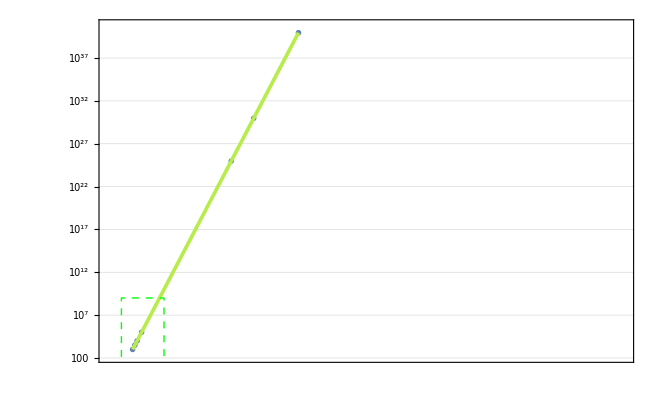
-Graphics--Graphics-

Chart printing:	done in 0.140608 sec

Overall computing time:	1.74265 sec

For detailed fits informations: type 'fitsDetails[z]'

```mathematica
(*computation cell - don't make any changes unless you know exactly what you are doing*)
startTime = AbsoluteTime[]; startTime = Table[startTime, {i, 2}];
settingsReady=True; computeReady=True;
(*================ DOSTOSOWANIE I WYKRYCIE NIEPRAWIDŁOWOŚCI W PARAMETRACH STERUJĄCYCH ================*)
For[z=1,z≤plotGroups,z++,
   If[Length[scatter[z]]>1,scatter[z]=Sort[scatter[z]]]; 
   If[Length[splines[z]]>1,splines[z]=Sort[splines[z]]]
];
checkParam[parameter_,operator_]:=If[!ValueQ[parameter[2]],operator[parameter[2],parameter[1]]];
checkAllParams[parameters__]:=For[i=1,i<=Length[{parameters}],i++,checkParam[{parameters}[[i,1]],{parameters}[[i,2]]]];
checkFun[fun_]:=If[!ValueQ[fun[2][x]],fun[2][x_]:=fun[1][x]];
checkAllFuns[funs__]:=For[i=1,i<=Length[{funs}],i++,checkFun[{funs}[[i]]]];
If[plotGroups>1,
   checkAllParams[{xlsFileName,Set},{xlsLabels,Set},{xScale,Set},{yScale,Set},{plots,Set},{scatter,Set},{splines,Set},{fits,Set},{plotRange,Set},{frameTicks,Set},{gridLines,Set},
                  {colorsListScatter,SetDelayed},{colorsListSplines,SetDelayed},{colorsListFits,SetDelayed},{markersTable,Set},{interpolationOrder,Set},{splinesFilling,Set},
                  {fitApparently,Set},{fitsFilling,Set},{fitsMethod,Set},{additionalPlotsRelativePosition,Set},{additionalPlotsOnInsets,Set},{additionalGraphicsRelativePosition,Set},
                  {additionalGraphicsOnInsets,Set},{labeledArrowsStylesAndFonts,Set},{legendDescriptionsSpaceForMissingPlots,Set},{legendDescriptionsAutomaticFits,Set}];
   If[!ValueQ[legendDescriptionsList[2]] && legendDescriptionsList[1]=!=Automatic,legendDescriptionsList[2]=Table[None,{i,Length[plots[2]]}]]; checkParam[legendDescriptionsList,Set];
   checkAllFuns[markerSize,splinesStyle,fitsStyle,fittingFunctions];
   If[!ValueQ[additionalPlots[2]],additionalPlots[2]=None];
   If[!ValueQ[additionalGraphics[2]],additionalGraphics[2]:=None];
   If[!ValueQ[legendAdditionalSymbols[2]],legendAdditionalSymbols[2]=None]
];
If[showPartComputingTimes, Print["Control parameters adjustation:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]; startTime[[1]] = AbsoluteTime[];


(*================ IMPORT DANYCH Z EXCELA ================*)
Print["Data import informations:"];
CheckAbort[noAbort=True;
MathPlot::lessPacksThanXlsFileNames="Found less packs of `4` (`1`) than xlsFiles to import (`2`). For all xlsFiles 1st `4` pack will be used (`3`).";
MathPlot::xlsLabelsNotFound = "Could not find any column matching `1` in `2` data region[`3`] in sheet `4` of '`5`'.";
MathPlot::xlsLabelsNotFoundAll = "Could not find any column group match in entire sheet-specification `1` of '`2`'. Aborting..."; 
MathPlot::notMachingListsXandY = "Number of columns labeled `1` is not equal to `2` nor are these columns in 'group' mode (`3` data region[`4`] in sheet `5` of '`6`').";
MathPlot::notMachingListsXandYAll = "Number of columns labeled `1` is not equal to `2` nor are these columns in 'group' mode in all data regions in sheet `3` of '`4`'. Aborting...";
MathPlot::notMachingListsYandΔY = "Number of columns labeled `1` is not equal to `2` in `3` data region[`4`] in sheet `5` of '`6`'. Dropping all `2` columns of this data region (plotting without error bars).";
MathPlot::tooLargeIndex = "Found `1` indexes in 'plots' larger than number of plots found in sheet `2` of '`3`'. Aborting...";
MathPlot::individualOrGroupArgumentInfo = "Treating `1` arguments (labeled: `2`) in `3` data region[`4`] in sheet `5` of '`6`' in `7` mode.";
MathPlot::noPairedData = "No paired data was found in columns `1`-`2`[`3`. imported dataset] in sheet `4` of '`5`'. In order not to mix styles/legends/etc., corresponding dataset was set to {{Null,Null}}.";
SetDirectory[NotebookDirectory[]];
For[z=1,z≤plotGroups,z++,
xlsFileNameNested[z]=If[Depth[xlsFileName[z]]==1,{xlsFileName[z]},xlsFileName[z]];
xlsLabelsNested[z]=If[Depth[xlsLabels[z]]==3 || Length[xlsLabels[z]]<Length[xlsFileNameNested[z]],
   If[Length[xlsFileNameNested[z]]>1,Message[MathPlot::lessPacksThanXlsFileNames,If[Depth[xlsLabels[z]]==3,1,Length[xlsLabels[z]]],Length[xlsFileNameNested[z]],MatrixForm[If[Depth[xlsLabels[z]]==3,xlsLabels[z],xlsLabels[z][[1]]]],"xlsLabels"]];
   Table[If[Depth[xlsLabels[z]]==3,xlsLabels[z],xlsLabels[z][[1]]],{i,Length[xlsFileNameNested[z]]}],
   xlsLabels[z]
];
plotsNested[z]=If[If[Length[Position[plots[z],All]]>0,Length[Position[plots[z],All][[1]]]==1,Max[Table[Length[Position[plots[z],_Integer][[i]]],{i,Length[Position[plots[z],_Integer]]}]]==2],
   {plots[z]},plots[z]];
plotsNested[z]=If[Length[plotsNested[z]]<Length[xlsFileNameNested[z]],
   If[Length[xlsFileNameNested[z]]>1,Message[MathPlot::lessPacksThanXlsFileNames,Length[plotsNested[z]],Length[xlsFileNameNested[z]],plotsNested[z][[1]],"plots"]];
   Table[plotsNested[z][[1]],{i,Length[xlsFileNameNested[z]]}],
   plotsNested[z]
];
For[i=1,i≤Length[plotsNested[z]],i++,For[j=1,j≤Length[plotsNested[z][[i]]],j+=2,
   If[Depth[plotsNested[z][[i,j]]]==1,
      plotsNested[z]=ReplacePart[plotsNested[z],{i,j}->{plotsNested[z][[i,j]],None}],
      If[Length[plotsNested[z][[i,j]]]==1,
         plotsNested[z]=ReplacePart[plotsNested[z],{i,j}->Append[plotsNested[z][[i,j]],None]]
      ]
   ]
]];

data[z]=leftCorner[z]=matchingColumns[z]=plotsData[z]=Table[{},{i,Length[xlsFileNameNested[z]]}];
For[file=1,file≤Length[xlsFileNameNested[z]],file++,
   For[i = 1, i <= Length[plotsNested[z][[file]]], i += 2,
      data[z]=ReplacePart[data[z],file->Append[data[z][[file]],If[NumericQ[plotsNested[z][[file,i,1]]],
         Import[xlsFileNameNested[z][[file]]][[plotsNested[z][[file,i,1]]]],
         Import[xlsFileNameNested[z][[file]]][[Position[Import[xlsFileNameNested[z][[file]],"Sheets"],plotsNested[z][[file,i,1]]][[1,1]]]]
      ]]];
      (*wyznaczenie początku danych*)
      leftCorner[z]=ReplacePart[leftCorner[z],file->Append[leftCorner[z][[file]], {{}}]];
      Quiet[If[plotsNested[z][[file,i,2,2]]===Equal,plotsNested[z]=ReplacePart[plotsNested[z],{file,i,2,2}->EqualTo]]];
      leftCornerPositions=Quiet[Position[data[z][[file,Length[data[z][[file]]]]],_?(plotsNested[z][[file,i,2,2]][plotsNested[z][[file,i,2,1]]])]];
      If[plotsNested[z][[file,i,2]]===None || Length[leftCornerPositions]==0,
         For[row = 1, row <= Length[data[z][[file,Length[data[z][[file]]]]]], row++,
            For[col = 1, col <= Length[data[z][[file,Length[data[z][[file]]], row]]], col++,
               If[Length[leftCorner[z][[file,Length[data[z][[file]]],1]]] == 0 && StringLength[data[z][[file,Length[data[z][[file]]], row, col]]] > 0, 
                  leftCorner[z]=ReplacePart[leftCorner[z],{file,Length[data[z][[file]]],1}->{row, col}];
                  col = Length[data[z][[file,Length[data[z][[file]]], row]]]; 
                  row = Length[data[z][[file,Length[data[z][[file]]]]]]
               ]
            ]
         ],
         leftCorner[z]=ReplacePart[leftCorner[z],{file,Length[data[z][[file]]]}->
            leftCornerPositions+Table[Which[
               plotsNested[z][[file,i,2,3]]===After,{0,1},
               plotsNested[z][[file,i,2,3]]===Below,{1,0},
               plotsNested[z][[file,i,2,3]]===Skew,{1,1}
            ],{j,Length[leftCornerPositions]}]]
      ];
      (*wyznaczenie indeksów kolumn do importu*)
      matchingColumns[z]=ReplacePart[matchingColumns[z],file->Append[matchingColumns[z][[file]],Table[{},{j,Length[leftCorner[z][[file,Length[data[z][[file]]]]]]},{i,Length[xlsLabelsNested[z][[file]]]}]]];
      For[lCIndex=1,lCIndex<=Length[leftCorner[z][[file,Length[data[z][[file]]]]]],lCIndex++,
         For[col=leftCorner[z][[file,Length[data[z][[file]]],lCIndex,2]],col<=Length[data[z][[file,Length[data[z][[file]]],leftCorner[z][[file,Length[data[z][[file]]],lCIndex,1]]]]], col++,
            If[data[z][[file,Length[data[z][[file]]],leftCorner[z][[file,Length[data[z][[file]]],lCIndex,1]],col]]≠"",
               For[test = 1, test <= Length[xlsLabelsNested[z][[file]]], test++,
                  If[xlsLabelsNested[z][[file,test,2]][ToString[data[z][[file,Length[data[z][[file]]],leftCorner[z][[file,Length[data[z][[file]]],lCIndex,1]],col]]], xlsLabelsNested[z][[file,test,1]]], 
                     matchingColumns[z]=ReplacePart[matchingColumns[z],{file,Length[data[z][[file]]],lCIndex,test}->Append[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,test]], col]]
                  ]
               ],
               Break[]
            ]
         ]
      ];
      Off[General::stop];
      atLeastOneColumnFoundInSheet=False;
      For[lCIndex=1,lCIndex<=Length[leftCorner[z][[file,Length[data[z][[file]]]]]],lCIndex++,
         testInRegion=True;
         For[j = 1, j <= Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]]], j++,
            If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,j]]] == 0, 
               If[j!=3,testInRegion=False]; (*w przypadku kolumny Δy niech również wyświetla się komunikat (poniżej), ale jej całkowity brak w Sheecie nie powinien generować Abortu. Ma to sens dla GŁÓWNYCH kolumn, ale dla błędu już nie - może w innym Sheecie taka kolumna się znajduje?*)
               Message[MathPlot::xlsLabelsNotFound,xlsLabelsNested[z][[file,j,1]],lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]],xlsFileNameNested[z][[file]]];
               Break[]
            ]
         ];
         If[testInRegion,atLeastOneColumnFoundInSheet=True]
      ];
      If[!atLeastOneColumnFoundInSheet,
         Message[MathPlot::xlsLabelsNotFoundAll,If[plotsNested[z][[file,i,2]]===None,MatrixForm[ReplacePart[plotsNested[z],{file,i,2}->"(automatically found data region)"][[file,i]]],MatrixForm[plotsNested[z][[file,i]]]],xlsFileNameNested[z][[file]]];
         Abort[]
      ];
      (*test poprawności danych x w stosunku do y*)
      correctDataRegion[z][file,(i+1)/2]={};
      For[lCIndex=1,lCIndex<=Length[leftCorner[z][[file,Length[data[z][[file]]]]]],lCIndex++,
         If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]] != Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]] && Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]] > 1 && Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]] > 1, 
            AppendTo[correctDataRegion[z][file,(i+1)/2],False];
            Message[MathPlot::notMachingListsXandY, xlsLabelsNested[z][[file,1, 1]], xlsLabelsNested[z][[file,2, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]]],
            AppendTo[correctDataRegion[z][file,(i+1)/2],True]
         ]
      ];
      If[!MemberQ[correctDataRegion[z][file,(i+1)/2],True],
         Message[MathPlot::notMachingListsXandYAll, xlsLabelsNested[z][[file,1, 1]], xlsLabelsNested[z][[file,2, 1]], plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]]];
         Abort[]
      ];
      (*test poprawności danych y w stosunku do Δy*)
      For[lCIndex=1,lCIndex<=Length[leftCorner[z][[file,Length[data[z][[file]]]]]],lCIndex++,
         If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]]] == 3 && Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]] != Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,3]]], 
            matchingColumns[z]=ReplacePart[matchingColumns[z],{file,Length[data[z][[file]]],lCIndex}->Drop[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]], -1]];
            Message[MathPlot::notMachingListsYandΔY, xlsLabelsNested[z][[file,2, 1]], xlsLabelsNested[z][[file,3, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]]]
         ]
      ];
      (*zamiana ewentualnych All na listy indeksów*)
      allPlotsInSheet=Table[j, {j, Sum[If[correctDataRegion[z][file,(i+1)/2][[j]],
         Max[Length[matchingColumns[z][[file,Length[data[z][[file]]],j,1]]],Length[matchingColumns[z][[file,Length[data[z][[file]]],j,2]]]],
         0
      ],{j,Length[leftCorner[z][[file,Length[data[z][[file]]]]]]}]}];
      If[plotsNested[z][[file,i + 1]] === All, 
         plotsNested[z]=ReplacePart[plotsNested[z],{file,i + 1}->allPlotsInSheet],
         numberOfTooLargeIndexes=Length[Select[plotsNested[z][[file,i + 1]],#>Length[allPlotsInSheet]&]];
         If[numberOfTooLargeIndexes>0,
            Message[MathPlot::tooLargeIndex,numberOfTooLargeIndexes,plotsNested[z][[file,i,1]],xlsFileNameNested[z][[file]]];
            Abort[]
         ]
      ];
      (*import danych do Appendowanej zmiennej plotsData*)
      oldLCIndex=-1; On[General::stop];
      For[col = 1, col <= Length[plotsNested[z][[file,i + 1]]], col++,
         (*transformacja indeksu w plotsNested na indeks leftCorner i index W leftCorner*)
         lCIndex=1; colInActLC=plotsNested[z][[file,i + 1,col]]; 
         While[colInActLC>(plotsInActRegion=If[correctDataRegion[z][file,(i+1)/2][[lCIndex]],
               Max[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]],Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]]],
               0]),
            colInActLC-=plotsInActRegion; lCIndex++
         ];
         If[oldLCIndex≠lCIndex,oldLCIndex=lCIndex;messageArgumentOut = False];
         (*rozpoznanie zespołowego/indywidualnego argumentu x/y*)
         Off[General::stop];
         xColumnIndexInMC = If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]] > 1, 
            (If[! messageArgumentOut, Message[MathPlot::individualOrGroupArgumentInfo, "X", xlsLabelsNested[z][[file,1, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]], "individual"]]; colInActLC(*plotsNested[z][[file,i + 1, col]]*)), 
            (If[! messageArgumentOut, Message[MathPlot::individualOrGroupArgumentInfo, "X", xlsLabelsNested[z][[file,1, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]], If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]] != Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]], "group", "single"]]]; 1)
         ];
         yColumnIndexInMC = If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]] > 1, 
            (If[! messageArgumentOut, Message[MathPlot::individualOrGroupArgumentInfo, "Y", xlsLabelsNested[z][[file,2, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]], "individual"]]; colInActLC(*plotsNested[z][[file,i + 1, col]]*)), 
            (If[! messageArgumentOut, Message[MathPlot::individualOrGroupArgumentInfo, "Y", xlsLabelsNested[z][[file,2, 1]], lCIndex,leftCorner[z][[file,Length[data[z][[file]]],lCIndex]],plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]], If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,1]]] != Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex,2]]], "group", "single"]]]; 1)
         ];
         messageArgumentOut = True; On[General::stop];
         actIndexesInMC = {xColumnIndexInMC, yColumnIndexInMC}; 
         If[Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]]] == 3,
            AppendTo[actIndexesInMC, colInActLC(*plotsNested[z][[file,i + 1, col]]*)] (*dla Δy nie ma rozpoznawania zespołowego/indywidualnego argumentu (działa WYŁĄCZNIE w trybie INDYWIDUALNYM/SINGLE)*)
         ]; 
         plotData = {};
         For[row = leftCorner[z][[file,Length[data[z][[file]]],lCIndex,1]] + 1, row <= Length[data[z][[file,Length[data[z][[file]]]]]], row++,
            rowData = Table[data[z][[file,Length[data[z][[file]]], row, matchingColumns[z][[file,Length[data[z][[file]]],lCIndex, j, actIndexesInMC[[j]]]]]], {j, Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]]]}];
            (*zakończ przy pierwszym pustym wierszu*)
            If[AllTrue[rowData,#==""&],Break[]];
            (*gdy brak pojedynczego Δy - nadanie mu wartości 0*)
            If[Length[rowData] == 3, 
               If[rowData[[3]] == "",rowData[[3]] = 0]
            ];
            (*dodawanie wyłącznie pełnych zespołów danych*)
            If[ToString[ToExpression[rowData[[1]]]] != "Null" && ToString[ToExpression[rowData[[2]]]] != "Null" && !MemberQ[rowData,$Failed], 
               AppendTo[plotData, rowData]
            ]
         ];
         Off[General::stop];
         If[Length[plotData] == 0,
            AppendTo[plotData, {Null,Null}];
            rowData = Table[data[z][[file,Length[data[z][[file]]], leftCorner[z][[file,Length[data[z][[file]]],lCIndex,1]], matchingColumns[z][[file,Length[data[z][[file]]], lCIndex,j, actIndexesInMC[[j]]]]]], {j, Length[matchingColumns[z][[file,Length[data[z][[file]]],lCIndex]]]}]; 
            Message[MathPlot::noPairedData, rowData[[1]], rowData[[2]], Length[plotsData[z][[file]]] + 1, plotsNested[z][[file,i,1]], xlsFileNameNested[z][[file]]]
         ];
         On[General::stop];
         plotsData[z]=ReplacePart[plotsData[z],file->Append[plotsData[z][[file]], plotData]]
      ]
   ]
];
bufferPlotsData={};
For[i=1,i≤Length[plotsData[z]],i++,bufferPlotsData=Join[bufferPlotsData,FlattenAt[Take[plotsData[z],{i,i}],1]]];
plotsData[z]=Table[SortBy[bufferPlotsData[[i]],First],{i,Length[bufferPlotsData]}] (*nieposortowane dane są problematyczne dla errorBarów i fillingów*)
];
If[showPartComputingTimes, Print["Data import:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]; startTime[[1]] = AbsoluteTime[];


(*================ AUTOMATYZACJA LABELI/LEGENDY/PLOTRANGE ================*)
(*legendLabels*)
For[z=1,z≤plotGroups,z++,If[!(legendPosition === None) && legendDescriptionsList[z] === Automatic,
   legendDescriptionsList[z] = {}; 
   For[file=1,file≤Length[xlsFileNameNested[z]],file++,
      For[i = 1, i <= Length[plotsNested[z][[file]]], i += 2,
         For[j = 1, j <= Length[plotsNested[z][[file,i + 1]]], j++,
            lCIndex=1; colInActLC=plotsNested[z][[file,i+1,j]]; 
            While[colInActLC>(plotsInActRegion=If[correctDataRegion[z][file,(i + 1)/2][[lCIndex]],
                  Max[Length[matchingColumns[z][[file,(i + 1)/2,lCIndex,1]]],Length[matchingColumns[z][[file,(i + 1)/2,lCIndex,2]]]],
                  0]),
               colInActLC-=plotsInActRegion; lCIndex++
            ];
            xOrYIndexInMC = If[Length[matchingColumns[z][[file,(i + 1)/2,lCIndex,2]]] > 1, 
               2, 
               If[Length[matchingColumns[z][[file,(i + 1)/2,lCIndex,1]]] > 1, 1, 2]
            ];
            AppendTo[legendDescriptionsList[z], data[z][[file,(i + 1)/2, leftCorner[z][[file,(i + 1)/2,lCIndex,1]], matchingColumns[z][[file,(i + 1)/2, lCIndex,xOrYIndexInMC, colInActLC(*plotsNested[z][[file,i + 1, j]]*)]]]]]
         ]
      ]
   ];
   legendDescriptionsList[z]=Join[legendDescriptionsList[z],Table["AddSym",{i,Length[legendAdditionalSymbols[z]]}]]
]];
(*plotRange*)
getPlotRange[z_Integer,sourcePlotRange_]:=(
   scales[z] = {xScale[z], yScale[z]}; 
   If[Length[plotRange[z]] == 0, 
      result=Table[If[scales[z][[k]] === Lin, Sort[sourcePlotRange[[k]] + 0.02*Table[(sourcePlotRange[[k, 2]] - sourcePlotRange[[k, 1]])*(-1)^l, {l, 2}]], Sort[E^(sourcePlotRange[[k]] + 0.02*Table[(sourcePlotRange[[k, 2]] - sourcePlotRange[[k, 1]])*(-1)^l, {l, 2}])]], {k, 2}];
      If[z>1 && xScale[1]===xScale[2],ReplacePart[result,1->plotRange[1][[1]]],result], 
      Table[If[Length[plotRange[z][[k]]] == 0, 
         If[k==1 && z>1 && xScale[1]===xScale[2],
            plotRange[1][[1]],
            If[scales[z][[k]] === Lin, Sort[sourcePlotRange[[k]] + 0.02*Table[(sourcePlotRange[[k, 2]] - sourcePlotRange[[k, 1]])*(-1)^l, {l, 2}]], Sort[E^(sourcePlotRange[[k]] + 0.02*Table[(sourcePlotRange[[k, 2]] - sourcePlotRange[[k, 1]])*(-1)^l, {l, 2}])]]
         ], 
         Sort[plotRange[z][[k]]]
      ], {k, 2}]
   ]
);
getPlotRangeFromMultiPlots[multiPlots_]:=(
   multiPlotsRanges=DeleteCases[Table[If[PlotRange[multiPlots[[i]]]≠{{0,1},{0,1}},PlotRange[multiPlots[[i]]]],{i,Length[multiPlots]}],Null];
   If[multiPlotsRanges=={},multiPlotsRanges={{0,1},{0,1}}];
   {{Min[Transpose[multiPlotsRanges][[1]]],Max[Transpose[multiPlotsRanges][[1]]]},
   {Min[Transpose[multiPlotsRanges][[2]]],Max[Transpose[multiPlotsRanges][[2]]]}}
);
maximizeRange[ranges_]:=If[Length[ranges]>0,
   {{Min[Transpose[ranges][[1]]],Max[Transpose[ranges][[1]]]},
    {Min[Transpose[ranges][[2]]],Max[Transpose[ranges][[2]]]}
   },
   Null
];


(*================ MARKERY ================*)
For[z=1,z≤plotGroups,z++,If[Length[markersTable[z]]==0,
   If[markersTable[z]===Automatic || markersTable[z]>Length[graphs],
      If[markersTable[z]>Length[graphs],Message[MathPlot::exceededLimitOfMarkers,Length[graphs]]];
      markersTable[z]=Length[graphs]
   ];
   markersTable[z]=Table[Mod[i-1,markersTable[z]]+1,{i,Length[plotsData[z]]}],
   If[Length[markersTable[z]]<Length[plotsData[z]],
      markersTable[z]=Table[markersTable[z][[Mod[i-1,Length[markersTable[z]]]+1]],{i,Length[plotsData[z]]}];
   ]
]];


(*================ UPERIODYCZNIANIE TABLIC ================*)
getPeriodic[periodicTable_,periodicLength_]:=(
   bufferTable=periodicTable;
   If[Length[bufferTable]==0, (*dostostosowanie periodicTable (zamiana wartości na periodyczną tablicę / periodyczne rozszerzenie tablicy / skrócenie zbyt długiej tablicy*)
      bufferTable=Table[bufferTable,{i, 1, periodicLength}],
      If[Length[bufferTable]<periodicLength,
         bufferTable=Table[bufferTable[[Mod[i-1,Length[bufferTable]]+1]],{i,periodicLength}],
         If[Length[bufferTable]>periodicLength,
            bufferTable=Take[bufferTable,periodicLength]
         ]
      ]
   ]; bufferTable
);
For[z=1,z≤plotGroups,z++,
   interpolationOrder[z]=getPeriodic[interpolationOrder[z],Length[plotsData[z]]];
   additionalPlotsOnInsets[z]=getPeriodic[additionalPlotsOnInsets[z],Length[additionalPlots[z]]];
   additionalGraphicsOnInsets[z]=getPeriodic[additionalGraphicsOnInsets[z],Length[additionalGraphics[z]]];
];


(*================ INICJALIZACJA GENERAL LISTPLOTA ================*)
For[z=1,z≤plotGroups,z++,plotFun[z] = If[xScale[z]=== Lin, 
   If[yScale[z] === Lin, ListPlot, ListLogPlot], 
   If[yScale[z] === Lin, ListLogLinearPlot, ListLogLogPlot]
]];
generalListPlot[z_Integer,dataSet_, dataSetIndex_, opts___] := If[Length[dataSet[[1]]] == 3, 
   singleErrListPlot[z,plotFun[z], dataSet, dataSetIndex, opts], 
   plotFun[z][dataSet, PlotMarkers -> marker[z,dataSetIndex, markerSize[z][dataSetIndex]], PlotRangePadding -> None, Axes -> None, opts]
];
singleErrListPlot[z_Integer,plotFun_, dataSet_, dataSetIndex_, opts___] := Block[{}, 
   plotFun[
      {{#[[1]], If[yScale[z]===Lin || #[[2]] - #[[3]]>0,#[[2]] - #[[3]],1*^-100]} & /@ dataSet, 
       {#[[1]], If[yScale[z]===Lin || #[[2]] + #[[3]]>0,#[[2]] + #[[3]],1*^-100]} & /@ dataSet, 
       dataSet[[;; , {1, 2}]]
      }, 
      Joined -> {False, False, False}, Filling -> {1 -> {2}}, FillingStyle -> Directive[Opacity[1], Thickness[0.001], 
      colorsListScatter[z][[dataSetIndex]]], 
      PlotMarkers -> {Graphics@{colorsListScatter[z][[dataSetIndex]], Thickness[0.001], Line[0.04 {{-1, 0}, {1, 0}}]}, Graphics@{colorsListScatter[z][[dataSetIndex]], Thickness[0.001], Line[0.04 {{-1, 0}, {1, 0}}]}, marker[z,dataSetIndex, markerSize[z][dataSetIndex]]}, 
      PlotRangePadding -> None, Axes -> None, Frame -> None, opts
   ]
];
If[showPartComputingTimes, Print["General setup:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]; startTime[[1]] = AbsoluteTime[];


(*================ WARSTWA: SCATTER[1] ================*)
setScatterPlot[z_]:={
   If[scatter[z] === All, 
      scatter[z] = Table[i, {i, Length[plotsData[z]]}], 
      If[scatter[z] === None, scatter[z] = {}]
   ];
   Quiet[Unset[scatterPlot[z]]; Clear[scatterPlot[z]]];
   If[Length[scatter[z]] > 0, 
      listOfScatterPlots=DeleteCases[Table[If[MemberQ[scatter[z],i],plotsData[z][[i]]],{i, 1, Length[plotsData[z]]}], Null];
      scatterPlots=Table[generalListPlot[z,listOfScatterPlots[[i]],scatter[z][[i]], PlotRange -> Full], {i, Length[scatter[z]]}];
      scatterPlot[z] = Show[scatterPlots, PlotRange -> plotRange[z], PlotRangePadding -> None];
      plotRangeScatter[z] = getPlotRangeFromMultiPlots[scatterPlots]
   ]
};
setScatterPlot[1];
If[showPartComputingTimes, Print["Main layers generation:"<>If[plotGroups<2,""," [1]"]]; If[Length[scatter[1]] > 0, Print["\t[scatter]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];


(*================ WARSTWA: SPLINES[1] ================*)
setSplinesPlot[z_]:={
   If[! (splines[z] === Null) || ! (fits[z] === Null),
      splinesPlotsData[z] = plotsData[z];
      For[i = 1, i <= Length[splinesPlotsData[z]], i++,
         For[j = 1, j <= Length[splinesPlotsData[z][[i]]], j++,
            If[Length[splinesPlotsData[z][[i, j]]] == 3, 
               splinesPlotsData[z]=ReplacePart[splinesPlotsData[z],{i,j}->Drop[splinesPlotsData[z][[i, j]],-1]]
            ]
         ]
      ]
   ];
   If[splines[z] === All, 
      splines[z] = Table[i, {i, Length[splinesPlotsData[z]]}], 
      If[splines[z] === None, splines[z] = {}]
   ];
   Quiet[Unset[splinesPlot[z]]; Clear[splinesPlot[z]]];
   If[Length[splines[z]] > 0, 
      If[MemberQ[splinesPlotsData[z],{{Null,Null}}],Off[ListPlot::iodeg]];
      splinesPlot[z] = plotFun[z][
         DeleteCases[Table[If[MemberQ[splines[z], i], splinesPlotsData[z][[i]]], {i, 1, Length[plotsData[z]]}], Null], 
         Joined -> True, InterpolationOrder -> Table[Table[interpolationOrder[z][[i]], {i, 1, Length[plotsData[z]]}][[splines[z][[j]]]], {j, Length[splines[z]]}], 
         PlotStyle -> Table[Table[Directive[splinesStyle[z][i], colorsListSplines[z][[i]]], {i, 1, Length[plotsData[z]]}][[splines[z][[j]]]], {j, Length[splines[z]]}], 
         PlotRange -> plotRange[z], Axes -> None, Frame -> None, Filling -> splinesFilling[z]
      ];
      If[MemberQ[splinesPlotsData[z],{{Null,Null}}],On[ListPlot::iodeg]];
      plotRangeSplines[z] = PlotRange[splinesPlot[z]]
   ]
};
setSplinesPlot[1];
If[showPartComputingTimes, If[Length[splines[1]] > 0, Print["\t[splines]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];


(*================ WARSTWA: FITS[1] ================*)
Clear[x];
transformedApparentFitPlotsData[z_Integer,i_,fitData_]:=If[!fitApparently[z][[i]] || (xScale[z]===Lin && yScale[z]===Lin),
   fitData,
   (transformedFitData=fitData;
   If[xScale[z]===Log,For[j=1,j≤Length[transformedFitData],j++,transformedFitData[[j,1]]=Log10[transformedFitData[[j,1]]]]];
   If[yScale[z]===Log,For[j=1,j≤Length[transformedFitData],j++,transformedFitData[[j,2]]=Log10[transformedFitData[[j,2]]]]];
   transformedFitData)
];
MathPlot::incorrectFitRange = "Incorrect format of fitting range has been detected for `1` fit (Automatic/Automatic[[1]]/Full/Full[[1]] probably due to Automated/Full plotRange specification and 'None' scatter or spline plot). All points will be considered for fits corresponding to these detections.";

setFitsPlot[z_Integer]:={
   plotRangeFits[z]=plotRange[z];
   finalPlotRanges[z]={};
   If[Length[scatter[z]]>0,AppendTo[finalPlotRanges[z],plotRangeScatter[z]]]; 
   If[Length[splines[z]]>0,AppendTo[finalPlotRanges[z],plotRangeSplines[z]]]; 
   If[Length[finalPlotRanges[z]]>0,plotRangeFits[z] = getPlotRange[z,maximizeRange[finalPlotRanges[z]]]];

   If[!(fits[z] === None), fitsPlotsData[z] = splinesPlotsData[z]];
   If[fits[z] === All, 
      fits[z]=Table[i,{i,Length[splinesPlotsData[z]]}], 
      If[fits[z] === None, fits[z] = {}]
   ];
   If[fitApparently[z]===False || fitApparently[z]===True,
      fitApparently[z]=Table[fitApparently[z],{i,Length[fittingFunctions[z][x]]}],
      If[Length[fitApparently[z]]<Length[fittingFunctions[z][x]],
         oldFALength=Length[fitApparently[z]];
         For[i=1,i<=Length[fittingFunctions[z][x]]-oldFALength,i++,
            AppendTo[fitApparently[z],fitApparently[z][[i]]];
         ]
      ]
   ];
   Quiet[
      fitsXRange = fitsXFittingRangeTableFunction[z];
      For[i = 1, i <= Length[fitsXRange], i++, 
         If[((fitsXRange[[i]] === Automatic || fitsXRange[[i]] === Full) && 
            !(plotRangeFits[z]===Automatic || plotRangeFits[z]===Full || plotRangeFits[z][[1]]===Automatic || plotRangeFits[z][[1]]===Full)),
            fitsXRange[[i]]=Sort[plotRangeFits[z][[1]]]
         ];
         If[fitsXRange[[i]] === Automatic || fitsXRange[[i]] === Full || fitsXRange[[i]] === Automatic[[1]] || fitsXRange[[i]] === Full[[1]], 
            Message[MathPlot::incorrectFitRange,i];
            fitsXRange[[i]]=All;
         ]
      ];
   ,{Part::partd}];
   fitsXSpanRange = fitsXSpanRangeTableFunction[z];
   fitsExpressions[z] = {};
   fitsXSpanRangeOnMaxMinScatter = {};

   For[i = 1, i <= Length[fits[z]], i++,
      If[!(fitsXRange[[i]] === All),
         For[j = 1, j <= Length[fitsPlotsData[z][[fits[z][[i]]]]], j++,
            If[fitsPlotsData[z][[fits[z][[i]], j, 1]] < fitsXRange[[i, 1]] || fitsPlotsData[z][[fits[z][[i]], j, 1]] > fitsXRange[[i, 2]], 
               fitsPlotsData[z]=ReplacePart[fitsPlotsData[z],fits[z][[i]]->Drop[fitsPlotsData[z][[fits[z][[i]]]], {j}]]; j--
            ]
         ]
      ];
      AppendTo[fitsXSpanRangeOnMaxMinScatter, Table[fitsPlotsData[z][[fits[z][[i]], 1, 1]], {j, 2}]];
      AppendTo[fitsExpressions[z], NonlinearModelFit[transformedApparentFitPlotsData[z,i,fitsPlotsData[z][[fits[z][[i]]]]],fittingFunctions[z][x][[i,1]],fittingFunctions[z][x][[i,2]],x,Method->fitsMethod[z]]];
      If[fitsXSpanRange[[i]] === Full, 
         If[Length[plotRangeFits[z]] == 2, 
            If[Length[plotRangeFits[z][[1]]]==2,
               fitsXSpanRange[[i]] = Sort[plotRangeFits[z][[1]]], 
               fitsXSpanRange[[i]] = Automatic
            ],
            fitsXSpanRange[[i]] = Automatic
         ]
      ];
      If[fitsXSpanRange[[i]] === Automatic,
         For[j = 2, j <= Length[fitsPlotsData[z][[fits[z][[i]]]]], j++,
            If[fitsXSpanRangeOnMaxMinScatter[[i,1]] > fitsPlotsData[z][[fits[z][[i]], j, 1]], 
               fitsXSpanRangeOnMaxMinScatter[[i,1]] = fitsPlotsData[z][[fits[z][[i]], j, 1]], 
               If[fitsXSpanRangeOnMaxMinScatter[[i,2]] < fitsPlotsData[z][[fits[z][[i]], j, 1]], 
                  fitsXSpanRangeOnMaxMinScatter[[i,2]] = fitsPlotsData[z][[fits[z][[i]], j, 1]]
               ]
            ]
         ];
         fitsXSpanRange[[i]] = fitsXSpanRangeOnMaxMinScatter[[i]]
      ];
      PrependTo[fitsXSpanRange[[i]],x]
   ];
   If[Length[fitsFilling[z]]==0,
      fitsFilling[z]=Table[fitsFilling[z],{i,Length[fits[z]]}],
      If[Length[fitsFilling[z]]<Length[fits[z]],
         oldFFLength=Length[fitsFilling[z]];
         For[i=1,i<=Length[fits[z]]-oldFFLength,i++,
            AppendTo[fitsFilling[z],fitsFilling[z][[i]]];
         ]
      ]
   ];
   Quiet[Unset[fitsPlot[z]]; Clear[fitsPlot[z]]];
   If[Length[fits[z]] > 0,
      fitPlotsData[z]=Table[
         If[!fitApparently[z][[i]] || (xScale[z]===Lin && yScale[z]===Lin),
            fitsExpressions[z][[i]]["BestFit"],
            (fitPlotData=If[yScale[z]===Log,10^fitsExpressions[z][[i]]["BestFit"],fitsExpressions[z][[i]]["BestFit"]];
            fitPlotData/.x->If[xScale[z]===Log,Log10[x],x])
         ],{i, Length[fits[z]]}
      ];
      fitsPlots=Table[plotFunExpression[z][
         fitPlotsData[z][[i]], 
         Evaluate[fitsXSpanRange[[i]]], 
         PlotStyle -> Table[Directive[fitsStyle[z][j], colorsListFits[z][[j]]], {j, 1, Length[plotsData[z]]}][[fits[z][[i]]]], 
         PlotRange -> plotRange[z], PlotRangePadding -> None, Axes -> None, Frame -> None, Filling -> fitsFilling[z][[i]]], {i, Length[fits[z]]}
      ];
      fitsPlot[z] = Show[fitsPlots];
      plotRangeFits[z] = getPlotRangeFromMultiPlots[fitsPlots];
      AppendTo[finalPlotRanges[z],plotRangeFits[z]]
   ]
};
setFitsPlot[1]; plotRange[1] = getPlotRange[1,maximizeRange[finalPlotRanges[1]]];
If[showPartComputingTimes, If[Length[fits[1]] > 0, Print["\t[fits]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];


(*================ WARSTWY: SCATTER[2],SPLINES[2],FITS[2] ================*)
If[plotGroups>1,  
   setScatterPlot[2];
   If[showPartComputingTimes, Print["Main layers generation: [2]"]; If[Length[scatter[2]] > 0, Print["\t[scatter]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];
   setSplinesPlot[2];
   If[showPartComputingTimes, If[Length[splines[2]] > 0, Print["\t[splines]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];
   setFitsPlot[2]; bufferPlotRange2=plotRange[2]; plotRange[2] = getPlotRange[2,maximizeRange[finalPlotRanges[2]]];
   If[showPartComputingTimes, If[Length[fits[2]] > 0, Print["\t[fits]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[],
   scatterPlot[2]=splinesPlot[2]=fitsPlot[2]={};
];


(*================ PASSE-PARTOUT ================*)
getGridLinesFromTicks[ticksTable_]:=If[Depth[ticksTable]<3,
   ticksTable,
   Table[If[Depth[ticksTable[[i]]]==1,
      ticksTable[[i]],
      ticksTable[[i,1]]
   ],{i,Length[ticksTable]}]
];
For[z=1,z≤plotGroups,z++,If[frameTicks[z]===None,frameTicks[z]=Table[None,{i,2},{j,2}]]; If[gridLines[z]===Automatic,
   gridLines[z]=If[frameTicks[z]===Automatic || frameTicks[z]===All,
      If[plotGroups>1,
         (frameTicks[z]=Switch[z,
            1,{{frameTicks[z],None},{frameTicks[z],None}},
            2,{{None,All},{None,If[plotRange[1][[1]]==plotRange[2][[1]] && xScale[1]===xScale[2],frameTicks[z],All]}}
         ];
         If[z==2 && plotRange[1][[1]]==plotRange[2][[1]] && xScale[1]===xScale[2],{None,Automatic},Automatic]),
         frameTicks[z]
      ],
      (
       For[i=1,i≤2,i++,For[j=1,j≤2,j++,
          gridLinesTable[i,j]=If[Depth[frameTicks[z][[i,j]]]>1,
             getGridLinesFromTicks[frameTicks[z][[i,j]]],
             frameTicks[z][[i,j]]
          ]
       ]];
       {If[(Depth[gridLinesTable[2,1]]==2 && !(gridLinesTable[2,1]===None)) || (Depth[gridLinesTable[2,2]]==2 && !(gridLinesTable[2,2]===None)),
           Join[
              Table[{gridLinesTable[2,2][[i]],Directive[Thickness[0.001], Magenta, Dotted]},{i,Length[gridLinesTable[2,2]]}],
              Table[{gridLinesTable[2,1][[i]],Directive[Thickness[0.001], Darker[Cyan], Dotted]},{i,Length[gridLinesTable[2,1]]}]
           ],
           If[!(gridLinesTable[2,1]===None) && !(gridLinesTable[2,2]===All),gridLinesTable[2,1],gridLinesTable[2,2]]
        ],
        If[(Depth[gridLinesTable[1,1]]==2 && !(gridLinesTable[1,1]===None)) || (Depth[gridLinesTable[1,2]]==2 && !(gridLinesTable[1,2]===None)),
           Join[
              Table[{gridLinesTable[1,2][[i]],Directive[Thickness[0.001], Magenta, Dotted]},{i,Length[gridLinesTable[1,2]]}],
              Table[{gridLinesTable[1,1][[i]],Directive[Thickness[0.001], Darker[Cyan], Dotted]},{i,Length[gridLinesTable[1,1]]}]
           ],
           If[!(gridLinesTable[1,1]===None) && !(gridLinesTable[1,2]===All),gridLinesTable[1,1],gridLinesTable[1,2]]
        ]
       }
      )
   ],
   If[z==2 && (frameTicks[z]===Automatic || frameTicks[z]===All),
      frameTicks[z]={{None,All},{None,If[plotRange[1][[1]]==plotRange[2][[1]] && xScale[1]===xScale[2],frameTicks[z],All]}}
   ]
]];

getFrameLabel[xlsLabelNested_]:=Switch[xlsLabelNested[[2]],
   StringStartsQ,xlsLabelNested[[1]]<>"^(*)",
   StringEndsQ,"^(*)"<>xlsLabelNested[[1]],
   StringContainsQ,"^(*)"<>xlsLabelNested[[1]]<>"^(*)",
   Equal,xlsLabelNested[[1]]
];
If[frameLabels === Automatic,
   frameLabelsFinal[1]=Table[getFrameLabel[xlsLabelsNested[1][[1,i]]], {i, 2}];
   If[plotGroups>1,
      frameLabelsFinal[2]={
         {None,getFrameLabel[xlsLabelsNested[2][[1,2]]]},
         {None,If[bufferPlotRange2===Automatic || bufferPlotRange2===Full || (Length[bufferPlotRange2]>1 && (bufferPlotRange2[[1]]===Automatic || bufferPlotRange2[[1]]===Full)),None,getFrameLabel[xlsLabelsNested[2][[1,1]]]]}
      }
   ],
   If[Depth[frameLabels]==2,
      If[Length[frameLabels]==2,
         frameLabelsFinal[1]=frameLabels; frameLabelsFinal[2]=None,
         frameLabelsFinal[1]=Drop[frameLabels,-1]; frameLabelsFinal[2]={{None,frameLabels[[3]]},{None,None}}
      ],
      If[plotGroups>1,
         frameLabelsFinal[1]={frameLabels[[2,1]],frameLabels[[1,1]]}; frameLabelsFinal[2]={{None,frameLabels[[1,2]]},{None,frameLabels[[2,2]]}},
         frameLabelsFinal[1]=frameLabels; frameLabelsFinal[2]=None
      ]
   ]
];
If[Depth[outputImageSize]==1,
   outputImageSize+=Sum[outputImagePadding[[1,i]],{i,2}],
   For[j=1,j≤2,j++,outputImageSize[[j]]+=Sum[outputImagePadding[[j,i]],{i,2}]]
];

For[z=1,z≤2,z++,Quiet[Unset[passePartOut[z]]; Clear[passePartOut[z]]]];
For[z=1,z≤plotGroups,z++,passePartOut[z] = With[
   {t = .001(*odsunięcie backgroundowej ramki od Frame'a*), 
    d = .5(*szerokość backgroundowej ramki naokoło Frame'a*), 
    background = White
   }, 
   plotFun[z][{0, 0}, FrameLabel -> frameLabelsFinal[z], LabelStyle -> labelStyle,
   Frame -> True, PlotRangePadding -> None, Axes -> None, 
   FrameTicks -> frameTicks[z], ImagePadding->outputImagePadding,
   GridLines -> gridLines[z], GridLinesStyle->Switch[z,1,Directive[Thickness[0.001], Darker[Cyan], Dotted],2,Directive[Thickness[0.001], Magenta, Dotted]],
   PlotRange -> plotRange[z], ImageSize -> outputImageSize, PlotStyle -> Opacity[0], 
   Epilog -> {background, FilledCurve[{{Line[ImageScaled /@ {{-d, -d}, {-d, 1 + d}, {1 + d, 1 + d}, {1 + d, -d}}]}, {Line[Scaled /@ {{-t, -t}, {-t, 1 + t}, {1 + t, 1 + t}, {1 + t, -t}}]}}]}]
]];
If[showPartComputingTimes, Print["Auxiliary layers generation:"]; Print["\t[passePartOut"<>If[plotGroups>1,"s",""]<>"]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]; startTime[[1]] = AbsoluteTime[];

passePartOutInset={}; 
For[i=1,i≤Length[insets],i++,If[insets[[i,1]]≤plotGroups,
   AppendTo[passePartOutInset,
      With[
         {t = .001(*odsunięcie backgroundowej ramki od Frame'a*), 
          d = .5(*szerokość backgroundowej ramki naokoło Frame'a*), 
          background = Opacity[0.04,insets[[i,5,1]]]
         }, 
         plotFun[insets[[i,1]]][{0, 0}, FrameLabel -> None, FrameStyle -> insets[[i,5]],
         Frame -> True, PlotRangePadding -> None, Axes -> None, 
         FrameTicks->If[insets[[i,7]]===Automatic,
            Switch[insets[[i,1]],
               1,{{insets[[i,7]],None},{insets[[i,7]],None}},
               2,{{None,All},If[!(frameTicks[2][[2,2]]===None) && !(frameTicks[2][[2,2]]===Automatic),{None,All},{insets[[i,7]],None}]}
            ],
            insets[[i,7]]
         ],
         GridLines -> insets[[i,8]], GridLinesStyle->Switch[insets[[i,1]],1,Directive[Thickness[0.001], Darker[Cyan], Dotted],2,Directive[Thickness[0.001], Magenta, Dotted]],
         PlotRange -> insets[[i,2]], (*ImageSize -> 500, *)PlotStyle -> Opacity[1], Background->background, AspectRatio->aspectRatio,
         Epilog -> {
            White,FilledCurve[{{Line[ImageScaled /@ {{-d, -d}, {-d, 1 + d}, {1 + d, 1 + d}, {1 + d, -d}}]}, {Line[Scaled /@ {{-t, -t}, {-t, 1 + t}, {1 + t, 1 + t}, {1 + t, -t}}]}}],
            background,FilledCurve[{{Line[ImageScaled /@ {{-d, -d}, {-d, 1 + d}, {1 + d, 1 + d}, {1 + d, -d}}]}, {Line[Scaled /@ {{-t, -t}, {-t, 1 + t}, {1 + t, 1 + t}, {1 + t, -t}}]}}]
         }]
      ]
   ]
]];
If[showPartComputingTimes, If[Length[insets]>0,Print["\t[passePartOut"<>If[Length[insets]>1,"s",""]<>"-inset"<>If[Length[insets]>1,"s",""]<>"]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[];


(*================ LEGEND ================*)
For[z=1,z≤plotGroups,z++,fitsDetailsIDs[z]={}];
If[!(legendPosition === None),
   getValidIndexesNormal[z_Integer,list_]:=(result={}; For[i=1,i≤Length[list],i++,descriptionIndexCounter=0; 
      For[j=1,j≤list[[i]],j++,descriptionIndexCounter++;
         If[StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"Space"] 
            || StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"Fit"]
            || StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"AddSym"],j--
         ]
      ];
      AppendTo[result,descriptionIndexCounter]
   ]; result);
   getValidIndexesSpecific[z_Integer,specifier_,list_]:=(result={}; descriptionIndexCounter=0; For[i=1,i≤Length[legendDescriptionsList[z]],i++,
      If[StringStartsQ[legendDescriptionsList[z][[i]],specifier],descriptionIndexCounter++;
         If[descriptionIndexCounter≤Length[list],
            AppendTo[result,i],
            Break[]
         ]
      ]
   ]; result);
   
   For[z=1,z≤plotGroups,z++,
   bufferFunList[z] = Table[{If[MemberQ[scatter[z],i],i,0],If[MemberQ[splines[z],i],i,0]}, {i, Length[plotsData[z]]}];
   For[i=Length[bufferFunList[z]],i≥1,i--,If[bufferFunList[z][[i]]=={0,0},bufferFunList[z]=Delete[bufferFunList[z],i]]];
   (*usunięcie (zamiana na Space) deskrypcji bazujących na zmiennej 'plots', przefiltrowanych przez zmienne scatter/splines
     ORAZ nadmiarowych deskrypcji Fitów (zdefiniowanych w legendDesciptionsList, ale w liczbie większej niż Length[fits])*)
   Quiet[
   finalFits[z]=fits[z];
   If[!(legendDescriptionsAutomaticFits[z]===None),
      legendDescriptionsList[z]=DeleteCases[legendDescriptionsList[z], _?(StringStartsQ["Fit"])];
      If[legendDescriptionsAutomaticFits[z]===First || legendDescriptionsAutomaticFits[z]===Last,
         fitsDescriptions={};
         For[i=1,i≤Length[finalFits[z]],i++,descriptionIndexCounter=0;
            For[j=1,j≤finalFits[z][[i]],j++,descriptionIndexCounter++;
               If[StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"Space"] || StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"AddSym"],j--]
            ];
            AppendTo[fitsDescriptions,"Fit:"<>legendDescriptionsAutomaticFitsDefaultLabel[z,i,If[legendDescriptionsList[z][[descriptionIndexCounter]]===None,"#"<>ToString[j-1]<>" dataset"<>If[plotGroups<2,""," ["<>ToString[z]<>"]"],legendDescriptionsList[z][[descriptionIndexCounter]]]]];
         ],
         If[Length[finalFits[z]]>1,finalFits[z]=Sort[finalFits[z]]]; 
         For[i=1,i≤Length[finalFits[z]],i++,descriptionIndexCounter=0;
            For[j=1,j≤finalFits[z][[i]],j++,descriptionIndexCounter++;
               If[StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"Space"] || StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"Fit"] || StringStartsQ[legendDescriptionsList[z][[descriptionIndexCounter]],"AddSym"],j--]
            ];
            legendDescriptionsList[z]=Insert[legendDescriptionsList[z],"Fit:"<>legendDescriptionsAutomaticFitsDefaultLabel[z,Position[fits[z],finalFits[z][[i]]][[1,1]],If[legendDescriptionsList[z][[descriptionIndexCounter]]===None,"#"<>ToString[j-1]<>" dataset"<>If[plotGroups<2,""," ["<>ToString[z]<>"]"],legendDescriptionsList[z][[descriptionIndexCounter]]]],descriptionIndexCounter+1];
         ]
      ]
   ];
   indexesOfValidDescriptionsScatter=getValidIndexesNormal[z,scatter[z]]; 
   indexesOfValidDescriptionsSplines=getValidIndexesNormal[z,splines[z]]; 
   indexesOfValidDescriptionsFits=getValidIndexesSpecific[z,"Fit",finalFits[z]]; 
   indexesOfValidDescriptionsAdditionalSymbols=getValidIndexesSpecific[z,"AddSym",legendAdditionalSymbols[z]]; 
   For[i=1,i≤Length[legendDescriptionsList[z]],i++,
      If[!MemberQ[indexesOfValidDescriptionsScatter,i] 
         && !MemberQ[indexesOfValidDescriptionsSplines,i] 
         && !MemberQ[indexesOfValidDescriptionsFits,i]
         && !MemberQ[indexesOfValidDescriptionsAdditionalSymbols,i]
         && (!StringStartsQ[legendDescriptionsList[z][[i]],"Space"] || legendDescriptionsList[z][[i]]===None),
            legendDescriptionsList[z]=ReplacePart[legendDescriptionsList[z],i->If[legendDescriptionsSpaceForMissingPlots[z],"Space","Space:n!o@n#e$"]] (*przypadek, gdy wykres jest wyfiltrowany (tj. jest w plots, ale nie ma go w scatter/splines) - nie ma go ani na obrazie ani w legendzie*)
      ]
   ];
   (*zlokalizowanie deskrypcji 'Space' & 'Fit' & 'AddSym'*)
   Which[
      legendDescriptionsAutomaticFits[z]===First,
         legendDescriptionsList[z]=Join[fitsDescriptions,legendDescriptionsList[z]],
      legendDescriptionsAutomaticFits[z]===Last,
         legendDescriptionsList[z]=Join[legendDescriptionsList[z],fitsDescriptions]
   ];
   spaceFitAddSymList = {};
   For[i = 1, i <= Length[legendDescriptionsList[z]], i++, 
      If[StringStartsQ[legendDescriptionsList[z][[i]], "Space"] 
         || StringStartsQ[legendDescriptionsList[z][[i]], "Fit"] 
         || StringStartsQ[legendDescriptionsList[z][[i]], "AddSym"], 
            AppendTo[spaceFitAddSymList, {i, legendDescriptionsList[z][[i]]}]
      ]
   ];
   (*usunięcie z listy deskrypcji 'Space' & 'Fit' & 'AddSym'*)
   legendDescriptionsList[z] = Take[DeleteCases[DeleteCases[DeleteCases[legendDescriptionsList[z],_?(StringStartsQ["Space"])],_?(StringStartsQ["Fit"])],_?(StringStartsQ["AddSym"])],Length[bufferFunList[z]]];
   If[legendDescriptionsList[z]==Null,legendDescriptionsList[z]={}];
   (*dodanie do listy deskrypcji opisów 'Space' (lub puste), 'Fit' (lub domyślne) i 'AddSym' (lub domyślne) oraz zidentyfikowanie ich jako '0' (lub finalFits[z][[i]]<>"f" lub addSymCounter<>"a") w bufferFunList*)
   fitCounter=0; addSymCounter=0;
   For[i = 1, i <= Length[spaceFitAddSymList], i++, 
      legendDescriptionsList[z] = Insert[legendDescriptionsList[z], 
         Which[
            spaceFitAddSymList[[i, 2]]=="Space:n!o@n#e$", 
               None, 
            StringStartsQ[spaceFitAddSymList[[i, 2]], "Space:"], 
               StringDrop[spaceFitAddSymList[[i, 2]], 6], 
            StringStartsQ[spaceFitAddSymList[[i, 2]], "Space"], 
               "",
            StringStartsQ[spaceFitAddSymList[[i, 2]], "Fit:"], 
               (fitCounter++; bufferFitID=StringDrop[spaceFitAddSymList[[i, 2]], 4];
               AppendTo[fitsDetailsIDs[z],bufferFitID]; (*tworzenie listy nazw na potrzeby fitsDetails[] (nie wystarczy na koniec sprawdzić i przefiltrować 'legendDescriptionsList[z]', bo przy użyciu 'manualnej' nazwy może nie dać się rozróżnić opisu fitu od pozostałych wykresów (niekoniecznie będzie posiadała np. "fit" w nazwie))*)
               bufferFitID), 
            StringStartsQ[spaceFitAddSymList[[i, 2]], "Fit"],
               (fitCounter++; bufferFitID="fit #"<>ToString[fitCounter]<>If[plotGroups<2,""," ["<>ToString[z]<>"]"];
               AppendTo[fitsDetailsIDs[z],bufferFitID]; (*j/w*)
               bufferFitID),
            StringStartsQ[spaceFitAddSymList[[i, 2]], "AddSym:"], 
               (addSymCounter++; StringDrop[spaceFitAddSymList[[i, 2]], 7]), 
            StringStartsQ[spaceFitAddSymList[[i, 2]], "AddSym"],
               (addSymCounter++; "additional symbol #"<>ToString[addSymCounter]<>If[plotGroups<2,""," ["<>ToString[z]<>"]"])
         ],
         spaceFitAddSymList[[i, 1]]
      ];
      bufferFunList[z] = Insert[bufferFunList[z], 
         {0,
          If[StringStartsQ[spaceFitAddSymList[[i, 2]],"Fit"],
            ToString[finalFits[z][[fitCounter]]]<>"f",
            If[StringStartsQ[spaceFitAddSymList[[i, 2]],"AddSym"],
               ToString[addSymCounter]<>"a",
               0
            ]
          ]
         }, 
         spaceFitAddSymList[[i, 1]]
      ]
   ];
   ,{StringStartsQ::strse}];
   (*usunięcie deskrypcji None*)
   For[i = Length[legendDescriptionsList[z]], i >= 1, i--, 
      If[legendDescriptionsList[z][[i]] === None, 
         legendDescriptionsList[z] = Delete[legendDescriptionsList[z], i]; 
         bufferFunList[z] = Delete[bufferFunList[z], i]
      ]
   ]];
   legendDescriptionsListFinal={};
   For[z=1,z≤plotGroups,z++,legendDescriptionsListFinal=Join[legendDescriptionsListFinal,legendDescriptionsList[z]]];
   legendOptions = {
      PlotLegends -> Placed[LineLegend[
         legendDescriptionsListFinal, LegendLayout -> legendLayout, LegendFunction -> legendFunction,
         Spacings->legendSpacings], If[legendPosition === In, legendInScaledPosition, {0, 0}]
      ], 
      LabelStyle -> legendLabelStyle, PlotRangePadding -> None, Axes -> None, Frame -> False, PlotRange -> plotRange[1], ImagePadding -> None
   };
   finalPlotLegendMarkers={};
   For[z=1,z≤plotGroups,z++,If[Length[scatter[z]] > 0 || Length[splines[z]] > 0 || Length[finalFits[z]] > 0, 
      referenceMaxSize=Max[Table[markerSize[z][i],{i,Length[plotsData[z]]}]];
      plotMarkersTable=Table[marker[z,i,markerSize[z][i]], {i, 1, Length[plotsData[z]]}];
      plotLegendMarkers=Table[If[bufferFunList[z][[j,1]]==0 && bufferFunList[z][[j,2]]==0,
            {Graphics[Text[""]],legendElementSize/10+j*10^-10(*PlotMarkers ma jakiś problem z IDENTYCZNYMI elementami typu "" gdy są jeden-po-drugim*)}, 
            (finalMarker=If[bufferFunList[z][[j,1]]>0,plotMarkersTable[[bufferFunList[z][[j,1]]]],Graphics[{},markerOptions]];
             If[StringEndsQ[ToString[bufferFunList[z][[j,2]]],"f"],
                finalLineStyle=fitsStyle[z]; finalLineColor=colorsListFits[z];
                bufferFunList[z]=ReplacePart[bufferFunList[z],{j,2}->ToExpression[StringDrop[bufferFunList[z][[j,2]],-1]]],
                finalLineStyle=splinesStyle[z]; finalLineColor=colorsListSplines[z]
             ];
             finalMarker[[1]]=If[StringEndsQ[ToString[bufferFunList[z][[j,2]]],"a"],
                (bufferFunList[z]=ReplacePart[bufferFunList[z],{j,2}->ToExpression[StringDrop[bufferFunList[z][[j,2]],-1]]];
                 legendAdditionalSymbols[z][[bufferFunList[z][[j,2]]]]
                ),
                Join[
                   If[bufferFunList[z][[j,2]]>0,
                      {Directive[Join[
                       getLegendSplinesDirectives[finalLineStyle,bufferFunList[z][[j,2]]],
                       {finalLineColor[[bufferFunList[z][[j,2]]]]}]],
                       Line[{{markerOptions[[1,2,1,1]],0},{markerOptions[[1,2,1,2]],0}}],
                       Dashing[None]
                      },
                      {}
                   ],
                   If[finalMarker[[1]]===None,
                      {},
                      finalMarker[[1]]
                   ]
                ]
             ];
             {finalMarker(*Append[finalMarker,ImagePadding->legendElementSizeVariationFactor*(1/markerSize[bufferFunList[[j,1]]]-1/referenceMaxSize)]*),legendElementSize/10}
            )
         ], {j, Length[bufferFunList[z]]}];
      ]; finalPlotLegendMarkers=Join[finalPlotLegendMarkers,plotLegendMarkers]
   ];
   AppendTo[legendOptions,PlotMarkers -> finalPlotLegendMarkers];
   If[legendPosition === In,
      legendIn=Null; For[z=1,z≤plotGroups,z++, 
         If[Length[bufferFunList[z]] > 0, 
            legendIn = plotFun[z][Table[{{∞, ∞}}, {i, Length[If[plotGroups>1,Join[bufferFunList[1],bufferFunList[2]],bufferFunList[1]]]}], legendOptions];
            Break[]
         ]
      ]; 
      legendOut =.,
      legendIn =.; 
      legendOut=Null; For[z=1,z≤plotGroups,z++, 
         If[Length[bufferFunList[z]] > 0, 
            legendOut = plotFun[z][Table[{{∞, ∞}}, {i, Length[If[plotGroups>1,Join[bufferFunList[1],bufferFunList[2]],bufferFunList[1]]]}], legendOptions][[2, 1]];
            Break[]
         ]
      ]; 
   ];
   
   If[showPartComputingTimes, If[Length[bufferFunList[1]] > 0 || Length[bufferFunList[2]] > 0, Print["\t[legend]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]]; startTime[[1]] = AbsoluteTime[], 
   legendIn =.; legendOut =.
];
,noAbort=False];


(*================ MERGE WARSTW I EXPORT ================*)
deleteNullWarstwy[layers_]:=(resultLayers=layers; For[i = 1, i ≤ Length[resultLayers], i++, 
   If[Length[resultLayers[[i]]] ≤ 1, resultLayers = Delete[resultLayers, i]; i--]
]; resultLayers);
For[z=1,z≤2,z++,warstwy[z] = {passePartOut[z], splinesPlot[z], scatterPlot[z], fitsPlot[z]}];
For[z=1,z≤2,z++,
   warstwy[z] = deleteNullWarstwy[warstwy[z]];
   If[Length[insets] > 0, templateWarstwInsets[z] = deleteNullWarstwy[{splinesPlot[z],scatterPlot[z],fitsPlot[z]}]]
];

For[z=1,z≤plotGroups,z++,If[Length[additionalPlots[z]] > 0,
   If[additionalPlotsRelativePosition[z] === Above, 
      AppendTo[warstwy[z], additionalPlots[z]];
      If[Length[insets] > 0, AppendTo[templateWarstwInsets[z], Pick[additionalPlots[z],additionalPlotsOnInsets[z]]]], 
      If[additionalPlotsRelativePosition[z] === Below, 
         warstwy[z] = Insert[warstwy[z], additionalPlots[z], 2];
         If[Length[insets] > 0, PrependTo[templateWarstwInsets[z], Pick[additionalPlots[z],additionalPlotsOnInsets[z]]]]
      ]
   ]
]];
For[z=1,z≤plotGroups,z++,If[Length[additionalGraphics[z]] > 0, 
   If[additionalGraphicsRelativePosition[z] === Above, 
      AppendTo[warstwy[z], Graphics[additionalGraphics[z]]];
      If[Length[insets] > 0, AppendTo[templateWarstwInsets[z], Graphics[Pick[additionalGraphics[z],additionalGraphicsOnInsets[z]]]]], 
      If[additionalGraphicsRelativePosition[z] === Below, 
         warstwy[z] = Insert[warstwy[z], Graphics[additionalGraphics[z]], 2];
         If[Length[insets] > 0, PrependTo[templateWarstwInsets[z], Graphics[Pick[additionalGraphics[z],additionalGraphicsOnInsets[z]]]]]
      ]
   ]
]];
insetsEpilog=(Epilog->
   (bufferEpilogTable=Table[If[insets[[i,1]]≤plotGroups,
      Inset[Show[Prepend[templateWarstwInsets[insets[[i,1]]],passePartOutInset[[i]]]],insets[[i,3,1]],insets[[i,3,2]],insets[[i,4]],Background->White],
      None
    ],{i,Length[insets]}];
    DeleteCases[bufferEpilogTable,None]
   )
);
For[i = 1, i ≤ Length[insets], i++, If[insets[[i,1]]≤plotGroups, AppendTo[warstwy[insets[[i,1]]],
   Graphics[{
      insets[[i,5,1]],insets[[i,6]],
      (transformedInsetRange={scaleDepLog[scales[insets[[i,1]]][[1]],insets[[i,2,1]]],scaleDepLog[scales[insets[[i,1]]][[2]],insets[[i,2,2]]]}; 
       Line[{{transformedInsetRange[[1,1]],transformedInsetRange[[2,1]]},{transformedInsetRange[[1,2]],transformedInsetRange[[2,1]]},
             {transformedInsetRange[[1,2]],transformedInsetRange[[2,2]]},{transformedInsetRange[[1,1]],transformedInsetRange[[2,2]]},
             {transformedInsetRange[[1,1]],transformedInsetRange[[2,1]]}}]
      )
   }]
]]];
If[noAbort,startTime[[1]] = AbsoluteTime[]; wykres = If[legendPosition === Out,
   Legended[Overlay[If[plotGroups<2,
      {Show[warstwy[1],AspectRatio->aspectRatio,insetsEpilog]},
      {Show[warstwy[1],AspectRatio->aspectRatio],
       Show[warstwy[2],AspectRatio->aspectRatio,insetsEpilog]
      }
   ]], Placed[legendOut, legendOutRelativePosition]],
   Overlay[If[plotGroups<2,
      {Show[If[legendPosition===In,Join[warstwy[1],{legendIn}],warstwy[1]],AspectRatio->aspectRatio,insetsEpilog]},
      {Show[warstwy[1],AspectRatio->aspectRatio],
       Show[If[legendPosition===In,Join[warstwy[2],{legendIn}],warstwy[2]],AspectRatio->aspectRatio,insetsEpilog]
      }
   ]]
]]
If[noAbort,
   chartPrintingTime = AbsoluteTime[] - startTime[[1]];
   If[showPartComputingTimes, Print[Style["Chart printing:\tdone in " <> ToString[DecimalForm[N[chartPrintingTime]]] <> " sec",If[chartPrintingTime>0.2,Red,Black]]]]; startTime[[1]] = AbsoluteTime[];
   If[!(exportFileName===None), 
      If[Depth[exportFileName]>1 && Length[exportFileName]==1,exportFileName=exportFileName[[1]]];
      If[Depth[exportFileName]==1,
         Export[exportFileName, wykres], 
         Export[exportFileName[[1]], wykres,exportFileName[[2]]] 
      ];
      If[showPartComputingTimes, Print["Chart exporting [" <> If[Depth[exportFileName]==1,exportFileName,exportFileName[[1]]] <> "]:\tdone in " <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[1]]]]] <> " sec"]]
   ];
   Print["Overall computing time:\t" <> ToString[DecimalForm[N[AbsoluteTime[] - startTime[[2]]]]] <> " sec"];
   If[Length[fits[1]]>0 || (plotGroups>1 && Length[fits[2]]>0),Print[Style["For detailed fits informations: type 'fitsDetails[z]'",Red]]]
];
```

### MathPlot Manipulate #1 - pointer-central zooming

```mathematica
(*computation cell - don't make any changes unless you know exactly what you are doing*)
computeReady=True;
Check[
For[z=1,z≤plotGroups,z++,If[ValueQ[xlsFileName[z]],
   defaultPlotRange[z]=plotRange[z];
   pointerRange[z]={
      {scaleDepLog[xScale[z],defaultPlotRange[z][[1,1]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,1]]]},
      {scaleDepLog[xScale[z],defaultPlotRange[z][[1,2]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,2]]]}
   };
   pointerCoords[z]={
      Mean[{scaleDepLog[xScale[z],defaultPlotRange[z][[1,1]]],scaleDepLog[xScale[z],defaultPlotRange[z][[1,2]]]}],
      Mean[{scaleDepLog[yScale[z],defaultPlotRange[z][[2,1]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,2]]]}]
   };
   actualScalePercents[z]=actualScaleFunctionShift[z]={1,1}; scaleFunctionMod[z]=3.5;
   actualScaleRange[z]=scaleRange[z,actualScalePercents[z],{scaleDepE[xScale[z],pointerCoords[z][[1]]],scaleDepE[yScale[z],pointerCoords[z][[2]]]},defaultPlotRange[z]];
   zoom2DSaved[z]={1/4,1/4},
   Message[MathPlot::plotUninitialized]
]];
If[!ValueQ[copyPointerPosition],copyPointerPosition="off"];
If[!ValueQ[activePlot] || plotGroups<2, activePlot=1];
frameTicksAdjustedLinLog[1]={{If[yScale[1]===Lin,Automatic,Charting`ScaledTicks[{Log,Exp}]],None},{If[xScale[1]===Lin,Automatic,Charting`ScaledTicks[{Log,Exp}]],None}};
If[plotGroups>1,frameTicksAdjustedLinLog[2]={{None,If[yScale[2]===Lin,All,Charting`ScaledTicks[{Log,Exp}]]},{None,If[xScale[2]===Lin,All,Charting`ScaledTicks[{Log,Exp}]]}}];
For[z=1,z≤plotGroups,z++,gridLinesAdjustedLinLog[z]=Table[If[scales[z][[i]]===Lin,Automatic,Charting`ScaledTickValues[{Log,Exp}]],{i,2}]];

Manipulate[Quiet[Check[
   oldScalePercents[activePlot]=actualScalePercents[activePlot];
   If[oldActivePlot≠activePlot,zoom2D=zoom2DSaved[activePlot]];
   If[!StringMatchQ[set100PercentScale,""],
      zoom2D={1/4,1/4};
      actualScaleFunctionShift[activePlot]={1,1};
      set100PercentScale=""
   ];
   If[!StringMatchQ[copyActualPlotRange,""],
      CopyToClipboard[Table[scaleDepE[scales[activePlot][[i]],actualScaleRange[activePlot][[i]]],{i,2}]];
      copyActualPlotRange=""
   ];
   If[!StringMatchQ[createPlotInset,""],
      CopyToClipboard["plotInset["<>ToString[activePlot]<>","<>ToString[InputForm[Table[scaleDepE[scales[activePlot][[i]],actualScaleRange[activePlot][[i]]],{i,2}]]]<>",{Scaled[(*coordsOfMainPlotPoint*){0.98,0.07}],Scaled[(*coordsOfInsetPoint*){1,0}]},(*size*)Scaled[0.4],(*frameStyle*)Directive[Red,8,FontFamily→\"Cambria\"],(*mainPlotRegionDashing - Dashing[None] for continuous line*)Dashed,(*frameTicks*)Automatic,(*gridLines*)Automatic]"];
      createPlotInset=""
   ];
   actualScalePercents[activePlot]=scaleFunction[zoom2D,actualScaleFunctionShift[activePlot],scaleFunctionMod[activePlot]];
   If[oldScalePercents[activePlot]≠actualScalePercents[activePlot] || oldActivePlot≠activePlot,
      actualScaleRange[activePlot]=scaleRange[activePlot,actualScalePercents[activePlot],{scaleDepE[xScale[activePlot],pointerCoords[activePlot][[1]]],scaleDepE[yScale[activePlot],pointerCoords[activePlot][[2]]]},defaultPlotRange[activePlot]];
      bufferRange=Table[If[actualScalePercents[activePlot][[i]]≥1,actualScaleRange[activePlot][[i]],scaleDepLog[scales[activePlot][[i]],defaultPlotRange[activePlot][[i]]]],{i,2}];
      pointerRange[activePlot]=Table[{bufferRange[[1,i]],bufferRange[[2,i]]},{i,2}];
   ];
   If[!StringMatchQ[exportSnapshot,""],
      timeStamp=IntegerString[Date[][[1]],10,4]<>IntegerString[Date[][[2]],10,2]<>IntegerString[Date[][[3]],10,2]<>"_"<>IntegerString[Date[][[4]],10,2]<>"."<>IntegerString[Date[][[5]],10,2]<>"."<>IntegerString[Floor[Date[][[6]]],10,2];
      If[exportFileName===None,
         snapshotFileName="mathPlot_snapshot-"<>timeStamp<>".pdf",
         finalExportFileName=If[Depth[exportFileName]==1,exportFileName,exportFileName[[1]]];
         snapshotFileName=StringTake[finalExportFileName,Last[StringPosition[finalExportFileName,"."]][[1]]-1]<>"_snapshot-"<>timeStamp<>StringTake[finalExportFileName,Last[StringPosition[finalExportFileName,"."]][[1]]-StringLength[finalExportFileName]-1]
      ];
      graphToExport=If[legendPosition === Out,
         Legended[Overlay[If[plotGroups<2,
            {Show[warstwy[1],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[warstwy[2],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]], Placed[legendOut, legendOutRelativePosition]],
         Overlay[If[plotGroups<2,
            {Show[If[legendPosition===In,Join[warstwy[1],{legendIn}],warstwy[1]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[If[legendPosition===In,Join[warstwy[2],{legendIn}],warstwy[2]],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]]
      ];
      If[Depth[exportFileName]==1,
         Export[snapshotFileName,graphToExport],
         Export[snapshotFileName,graphToExport,exportFileName[[2]]]
      ];
      exportSnapshot=""
   ];

   Manipulate[
      oldActivePlot=activePlot;
      pointerCoords[activePlot]=u;
      showPointerCoordinatesStarter=showPointerCoordinates;
      showMagnificationLevelStarter=showMagnificationLevel;
      actualScaleRange[activePlot]=scaleRange[activePlot,actualScalePercents[activePlot],{scaleDepE[xScale[activePlot],pointerCoords[activePlot][[1]]],scaleDepE[yScale[activePlot],pointerCoords[activePlot][[2]]]},defaultPlotRange[activePlot]];
      If[!StringMatchQ[slopeScale,""],
         If[StringMatchQ[slopeScale,"decrease"],
            scaleFunctionMod[activePlot]/=2,
            If[StringMatchQ[slopeScale,"increase"],scaleFunctionMod[activePlot]*=2]
         ];
         actualScaleFunctionShift[activePlot]=actualScalePercents[activePlot];
         zoom2D={1/4,1/4}+RandomReal[{1*^-10,1*^-9}]
      ];
      If[!StringMatchQ[resetPointerScale,""],
         For[i=1,i≤2,i++,
            If[actualScalePercents[activePlot][[i]]<=1,
               For[j=1,j≤2,j++,defaultPlotRange[activePlot]=ReplacePart[defaultPlotRange[activePlot],{i,j}->scaleDepE[scales[activePlot][[i]],actualScaleRange[activePlot][[i,j]]]]];
               zoom2D[[i]]=1/4
            ]
         ];
         zoom2D+=RandomReal[{1*^-10,1*^-9}]
      ];
      zoom2DSaved[activePlot]=zoom2D;
      If[StringMatchQ[copyPointerPosition,"real"],
         CopyToClipboard[Table[scaleDepE[scales[activePlot][[i]],pointerCoords[activePlot][[i]]],{i,2}]],
         If[StringMatchQ[copyPointerPosition,"scaled global"],
            CopyToClipboard[Scaled[{Rescale[pointerCoords[activePlot][[1]],scaleDepLog[xScale[activePlot],defaultPlotRange[activePlot][[1]]]],Rescale[pointerCoords[activePlot][[2]],scaleDepLog[yScale[activePlot],defaultPlotRange[activePlot][[2]]]]}]]
         ]
      ];
      prologBuffer=(Prolog->{Dashed,
         If[actualScalePercents[activePlot][[2]]≥1,Green,Red],Line[{pointerRange[activePlot][[1]],{pointerRange[activePlot][[2,1]],pointerRange[activePlot][[1,2]]}}],Line[{{pointerRange[activePlot][[2,1]],pointerRange[activePlot][[2,2]]},{pointerRange[activePlot][[1,1]],pointerRange[activePlot][[2,2]]}}],
         If[actualScalePercents[activePlot][[1]]≥1,Green,Red],Line[{{pointerRange[activePlot][[2,1]],pointerRange[activePlot][[1,2]]},{pointerRange[activePlot][[2,1]],pointerRange[activePlot][[2,2]]}}],Line[{{pointerRange[activePlot][[1,1]],pointerRange[activePlot][[2,2]]},pointerRange[activePlot][[1]]}]
      });
      epilogBuffer=(Epilog->{
         If[showPointerCoordinates,
            {Text[Style[" X:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[xScale[activePlot],pointerCoords[activePlot][[1]]],10]]]<>"  ("<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[1]],scaleDepLog[xScale[activePlot],defaultPlotRange[activePlot][[1]]]]],{4,3}]]<>")",Black],Scaled[{0,0.055}],{-1,-1},Background->Pink],
             Text[Style[" Y:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[yScale[activePlot],pointerCoords[activePlot][[2]]],10]]]<>"  ("<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[2]],scaleDepLog[yScale[activePlot],defaultPlotRange[activePlot][[2]]]]],{4,3}]]<>")",Black],Scaled[{0,0}],{-1,-1},Background->Pink]
            }
         ],
         If[showMagnificationLevel,
            {Text[Style["X:"<>ToString[DecimalForm[actualScalePercents[activePlot][[1]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[1]]≥1,Black,White]],Scaled[{1,0.05}],{1,-1},Background->If[actualScalePercents[activePlot][[1]]≥1 ,Green,Red]],
             Text[Style["Y:"<>ToString[DecimalForm[actualScalePercents[activePlot][[2]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[2]]≥1,Black,White]],Scaled[{1,0}],{1,-1},Background->If[actualScalePercents[activePlot][[2]]≥1,Green,Red]]
            }
         ]
      });
      If[legendPosition === Out,
         Legended[Overlay[If[plotGroups<2,
            {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,prologBuffer,epilogBuffer]},
            If[activePlot==1,
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,prologBuffer],
                Show[layers[2,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,epilogBuffer]
               },
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
                Show[layers[2,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,prologBuffer,epilogBuffer]
               }
            ]
         ]], Placed[legendOut, legendOutRelativePosition]],
         Overlay[If[plotGroups<2,
            {Show[If[legendPosition===In,Join[layers[1,activePlot,economicMode,pointerCoords[activePlot]],{legendIn}],layers[1,activePlot,economicMode,pointerCoords[activePlot]]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,prologBuffer,epilogBuffer]},
            If[activePlot==1,
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,prologBuffer],
                Show[If[legendPosition===In,Join[layers[2,activePlot,economicMode,pointerCoords[activePlot]],{legendIn}],layers[2,activePlot,economicMode,pointerCoords[activePlot]]],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,epilogBuffer]
               },
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->actualScaleRange[1],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
                Show[If[legendPosition===In,Join[layers[2,activePlot,economicMode,pointerCoords[activePlot]],{legendIn}],layers[2,activePlot,economicMode,pointerCoords[activePlot]]],PlotRange->actualScaleRange[2],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[actualScaleRange[1][[1]]==actualScaleRange[2][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,prologBuffer,epilogBuffer]
               }
            ]
         ]]
      ],
      Column[
         {Row[
            {Control[{{u,pointerCoords[activePlot],"Pointer"},pointerRange[activePlot][[1]],pointerRange[activePlot][[2]],Slider2D,ImageSize->{150,150}}],
             Control[{{resetPointerScale,"",""},{"reset scale"},Setter}]
            }
          ],
          Control[{{slopeScale,"","Zoom slope:"},{"decrease",ToString[NumberForm[scaleFunctionMod[activePlot],{5,2}]],"increase"},Setter}],
          Row[{"copy pointer's scaled position:  ",RadioButtonBar[Dynamic[copyPointerPosition],{"off","real","scaled global"}]}]
         },Left
      ], 
      TrackedSymbols:>{u,resetPointerScale,slopeScale,copyPointerPosition,showPointerCoordinates,showMagnificationLevel}
   ],
   Message[MathPlot::plotUninitialized]
]],
Column[
   {Control[{{zoom2D,{1/4,1/4},"Zoom X-Y"},Slider2D,ImageSize->{150,150}}],
    Row[
       {Control[{{set100PercentScale,"",""},{"100%"},Setter}],
        Control[{{copyActualPlotRange,"",""},{"copy PlotRange"},Setter}],
        Control[{{createPlotInset,"",""},{"copy plotInset"},Setter}]
       }
    ],
    Row[{"Active plot manipulation:  ",RadioButtonBar[Dynamic[activePlot],{1,2},Enabled->plotGroups>1]}],
    Control[{{showPointerCoordinates,If[ValueQ[showPointerCoordinatesStarter],showPointerCoordinatesStarter,True],"Show pointer's coordinates"},Checkbox}],
    Control[{{showMagnificationLevel,If[ValueQ[showMagnificationLevelStarter],showMagnificationLevelStarter,True],"Show magnification level"},Checkbox}],
    Row[
       {Control[{{economicMode,chartPrintingTime>0.2,"Economic mode"},Checkbox}],
        Control[{{exportSnapshot,""," "},{"export snapshot"},Setter}]
       }
    ]
   }
],ControlPlacement->Left, 
TrackedSymbols:>{zoom2D,set100PercentScale,exportSnapshot,copyActualPlotRange,createPlotInset,activePlot}]
,Message[MathPlot::plotUninitialized]]
```

### MathPlot Manipulate #2 - rectangular zooming

```mathematica
(*computation cell - don't make any changes unless you know exactly what you are doing*)
computeReady=True;
Check[
For[z=1,z≤plotGroups,z++,If[ValueQ[xlsFileName[z]],
   defaultPlotRange[z]=plotRange[z];
   pointerRange[z]={
      {scaleDepLog[xScale[z],defaultPlotRange[z][[1,1]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,1]]]},
      {scaleDepLog[xScale[z],defaultPlotRange[z][[1,2]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,2]]]}
   }; 
   pointerCoords[z]={
      Mean[{scaleDepLog[xScale[z],defaultPlotRange[z][[1,1]]],scaleDepLog[xScale[z],defaultPlotRange[z][[1,2]]]}],
      Mean[{scaleDepLog[yScale[z],defaultPlotRange[z][[2,1]]],scaleDepLog[yScale[z],defaultPlotRange[z][[2,2]]]}]
   };
   actualScalePercents[z]={1,1};
   scaleRanges[z][0]=Table[scaleDepLog[scales[z][[i]],defaultPlotRange[z][[i]]],{i,2}];
   actualScaleRangeIndex[z]=0; 
   If[NumericQ[maxScaleRangeIndex[z]], For[i=1,i≤maxScaleRangeIndex[z],i++,scaleRanges[z][i]=.]]; maxScaleRangeIndex[z]=0;
   paneSizeMod={200,aspectRatio*200};
   zoomRectBLSaved[z]={0,0}*paneSizeMod; zoomRectTRSaved[z]={1,1}*paneSizeMod;
   zoomRectBRSaved[z]={1,0}*paneSizeMod; zoomRectTLSaved[z]={0,1}*paneSizeMod,
   Message[MathPlot::plotUninitialized]
]]; 
If[!ValueQ[copyPointerPosition],copyPointerPosition="off"];
If[!ValueQ[activePlot] || plotGroups<2, activePlot=1];
frameTicksAdjustedLinLog[1]={{If[yScale[1]===Lin,Automatic,Charting`ScaledTicks[{Log,Exp}]],None},{If[xScale[1]===Lin,Automatic,Charting`ScaledTicks[{Log,Exp}]],None}};
If[plotGroups>1,frameTicksAdjustedLinLog[2]={{None,If[yScale[2]===Lin,All,Charting`ScaledTicks[{Log,Exp}]]},{None,If[xScale[2]===Lin,All,Charting`ScaledTicks[{Log,Exp}]]}}];
For[z=1,z≤plotGroups,z++,gridLinesAdjustedLinLog[z]=Table[If[scales[z][[i]]===Lin,Automatic,Charting`ScaledTickValues[{Log,Exp}]],{i,2}]];
zoomRectBL={0,0}*paneSizeMod; zoomRectTR={1,1}*paneSizeMod; zoomRectBR={1,0}*paneSizeMod; zoomRectTL={0,1}*paneSizeMod;
pointerPaneBackground:=ImageResize[Rasterize[
   Show[warstwy[activePlot],PlotRange->scaleRanges[activePlot][actualScaleRangeIndex[activePlot]],FrameTicks->frameTicksAdjustedLinLog[activePlot],GridLines->gridLinesAdjustedLinLog[activePlot],GridLinesStyle->Directive[Thickness[0.001],If[activePlot==1,Darker[Cyan],Magenta],Dotted],AspectRatio->aspectRatio,Frame->False,ImagePadding->False]
],paneSizeMod[[1]]];

Manipulate[Quiet[Check[
   oldScaleRangeIndex[activePlot]=actualScaleRangeIndex[activePlot];
   If[oldActivePlot≠activePlot,
      zoomRectBL=zoomRectBLSaved[activePlot];
      zoomRectTR=zoomRectTRSaved[activePlot];
      zoomRectBR=zoomRectBRSaved[activePlot];
      zoomRectTL=zoomRectTLSaved[activePlot]
   ];
   If[!StringMatchQ[scaleChange,""],
      If[StringMatchQ[scaleChange,"-"],
         actualScaleRangeIndex[activePlot]--,
         If[StringMatchQ[scaleChange,"100%"],
            scaleRanges[activePlot][0]=Table[scaleDepLog[scales[activePlot][[i]],defaultPlotRange[activePlot][[i]]],{i,2}];
            actualScaleRangeIndex[activePlot]=0; 
            For[i=1,i≤maxScaleRangeIndex[activePlot],i++,scaleRanges[activePlot][i]=.]; 
            maxScaleRangeIndex[activePlot]=0; 
            actualScalePercents[activePlot]={1,1}; 
            zoomRectBL={0,0}*paneSizeMod; zoomRectTR={1,1}*paneSizeMod;
            zoomRectBR={1,0}*paneSizeMod; zoomRectTL={0,1}*paneSizeMod,
            If[zoomRectBL≠{0,0}*paneSizeMod || zoomRectTR≠{1,1}*paneSizeMod, actualScaleRangeIndex[activePlot]++]
         ]
      ]; 
      scaleChange=""
   ];
   If[!StringMatchQ[copyActualPlotRange,""],
      CopyToClipboard[Table[scaleDepE[scales[activePlot][[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}]];
      copyActualPlotRange=""
   ];
   If[!StringMatchQ[createPlotInset,""],
      CopyToClipboard["plotInset["<>ToString[activePlot]<>","<>ToString[InputForm[Table[scaleDepE[scales[activePlot][[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}]]]<>",{Scaled[(*coordsOfMainPlotPoint*){0.98,0.07}],Scaled[(*coordsOfInsetPoint*){1,0}]},(*size*)Scaled[0.4],(*frameStyle*)Directive[Red,8,FontFamily→\"Cambria\"],(*mainPlotRegionDashing - Dashing[None] for continuous line*)Dashed,(*frameTicks*)Automatic,(*gridLines*)Automatic]"];
      createPlotInset=""
   ];
   If[oldScaleRangeIndex[activePlot]≠actualScaleRangeIndex[activePlot],
      If[actualScaleRangeIndex[activePlot]>oldScaleRangeIndex[activePlot],
         If[zoomRectBL≠{0,0}*paneSizeMod || zoomRectTR≠{1,1}*paneSizeMod,
            If[actualScaleRangeIndex[activePlot]>maxScaleRangeIndex[activePlot],
               maxScaleRangeIndex[activePlot]=actualScaleRangeIndex[activePlot];
               bufferNextScaleRange=.,
               bufferNextScaleRange=scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]
            ];
            scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]=Table[
               {getRealFromScaled[scales[activePlot][[i]],zoomRectBL[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]-1][[i]]],
                getRealFromScaled[scales[activePlot][[i]],zoomRectTR[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]-1][[i]]]
               },{i,2}
            ];
            scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]=Table[scaleDepLog[scales[activePlot][[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}];
            If[ValueQ[bufferNextScaleRange],
               If[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]!=bufferNextScaleRange,For[i=actualScaleRangeIndex[activePlot]+1,i≤maxScaleRangeIndex[activePlot],i++,scaleRanges[activePlot][i]=.];maxScaleRangeIndex[activePlot]=actualScaleRangeIndex[activePlot]]
            ];
         ],
         If[actualScaleRangeIndex[activePlot]<0,
            scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]=Table[
               {getRealFromScaled[scales[activePlot][[i]],-0.2,scaleRanges[activePlot][actualScaleRangeIndex[activePlot]+1][[i]]],
                getRealFromScaled[scales[activePlot][[i]],1.2,scaleRanges[activePlot][actualScaleRangeIndex[activePlot]+1][[i]]]
               },{i,2}
            ];
            scaleRanges[activePlot][actualScaleRangeIndex[activePlot]]=Table[scaleDepLog[scales[activePlot][[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}]
         ]
      ];
      If[actualScaleRangeIndex[activePlot]<maxScaleRangeIndex[activePlot],
         zoomRectBL=Table[Rescale[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]+1][[i,1]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}]*paneSizeMod;
         zoomRectTR=Table[Rescale[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]+1][[i,2]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}]*paneSizeMod,
         zoomRectBL={0,0}*paneSizeMod; zoomRectTR={1,1}*paneSizeMod
      ];
      zoomRectBR={zoomRectTR[[1]],zoomRectBL[[2]]}; zoomRectTL={zoomRectBL[[1]],zoomRectTR[[2]]};
      bufferRange=Table[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]],{i,2}];
      pointerRange[activePlot]=Table[{bufferRange[[1,i]],bufferRange[[2,i]]},{i,2}];
      actualScalePercents[activePlot]=Table[Differences[Table[scaleDepLog[scales[activePlot][[i]],defaultPlotRange[activePlot][[i]]],{i,2}][[j]]][[1]]/Differences[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[j]]][[1]],{j,2}]
   ];
   If[!StringMatchQ[exportSnapshot,""],
      timeStamp=IntegerString[Date[][[1]],10,4]<>IntegerString[Date[][[2]],10,2]<>IntegerString[Date[][[3]],10,2]<>"_"<>IntegerString[Date[][[4]],10,2]<>"."<>IntegerString[Date[][[5]],10,2]<>"."<>IntegerString[Floor[Date[][[6]]],10,2];
      If[exportFileName===None,
         snapshotFileName="mathPlot_snapshot-"<>timeStamp<>".pdf",
         finalExportFileName=If[Depth[exportFileName]==1,exportFileName,exportFileName[[1]]];
         snapshotFileName=StringTake[finalExportFileName,Last[StringPosition[finalExportFileName,"."]][[1]]-1]<>"_snapshot-"<>timeStamp<>StringTake[finalExportFileName,Last[StringPosition[finalExportFileName,"."]][[1]]-StringLength[finalExportFileName]-1]
      ];
      graphToExport=If[legendPosition === Out,
         Legended[Overlay[If[plotGroups<2,
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[warstwy[2],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]], Placed[legendOut, legendOutRelativePosition]],
         Overlay[If[plotGroups<2,
            {Show[If[legendPosition===In,Join[warstwy[1],{legendIn}],warstwy[1]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[If[legendPosition===In,Join[warstwy[2],{legendIn}],warstwy[2]],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]]
      ];
      If[Depth[exportFileName]==1,
         Export[snapshotFileName,graphToExport],
         Export[snapshotFileName,graphToExport,exportFileName[[2]]]
      ];
      exportSnapshot=""
   ];
   
   If[!vectorGraphicsMode,
      passePartOutWithMarkedDots={
         passePartOut[activePlot],
         Graphics[{PointSize[0.1],
            RGBColor[{1/255,2/255,3/255}],Point[Table[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i,1]],{i,2}]],
            RGBColor[{3/255,2/255,1/255}],Point[Table[scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i,2]],{i,2}]]
         }]
      };     
      passePartOutWithMarkedDotsAndLegend=Show[If[legendPosition === Out,
         Legended[passePartOutWithMarkedDots,Placed[legendOut,legendOutRelativePosition]], 
         passePartOutWithMarkedDots],
         PlotRange->scaleRanges[activePlot][actualScaleRangeIndex[activePlot]],
         AspectRatio->aspectRatio
      ];
      rasteredPassePartOutPixelData=Rasterize[passePartOutWithMarkedDotsAndLegend,"Data"];
      rasteredPassePartOutSize=Rasterize[passePartOutWithMarkedDotsAndLegend,"RasterSize"];
      rasteredWykres=Rasterize[If[legendPosition === Out,
         Legended[Overlay[If[plotGroups<2,
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[warstwy[2],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]], Placed[legendOut, legendOutRelativePosition]],
         Overlay[If[plotGroups<2,
            {Show[If[legendPosition===In,Join[warstwy[1],{legendIn}],warstwy[1]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio]},
            {Show[warstwy[1],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
             Show[If[legendPosition===In,Join[warstwy[2],{legendIn}],warstwy[2]],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio]
            }
         ]]
      ]];
      rasteredLeftBotCorner={Min[Transpose[Position[rasteredPassePartOutPixelData,{1,2,3}]][[2]]],rasteredPassePartOutSize[[2]]-Max[Transpose[Position[rasteredPassePartOutPixelData,{1,2,3}]][[1]]]}+{-1,1}*2;
      rasteredRightTopCorner={Max[Transpose[Position[rasteredPassePartOutPixelData,{3,2,1}]][[2]]],rasteredPassePartOutSize[[2]]-Min[Transpose[Position[rasteredPassePartOutPixelData,{3,2,1}]][[1]]]}+{0,1}*2;
   ];

   Manipulate[
      oldActivePlot=activePlot;
      pointerCoords[activePlot]=u;
      showPointerCoordinatesStarter=showPointerCoordinates;
      showMagnificationLevelStarter=showMagnificationLevel;
      If[StringMatchQ[copyPointerPosition,"real"],
         CopyToClipboard[Table[scaleDepE[scales[activePlot][[i]],pointerCoords[activePlot][[i]]],{i,2}]],
         If[StringMatchQ[copyPointerPosition,"scaled global"],
            CopyToClipboard[Scaled[{Rescale[pointerCoords[activePlot][[1]],scaleDepLog[xScale[activePlot],defaultPlotRange[activePlot][[1]]]],Rescale[pointerCoords[activePlot][[2]],scaleDepLog[yScale[activePlot],defaultPlotRange[activePlot][[2]]]]}]],
            If[StringMatchQ[copyPointerPosition,"scaled local"],
               CopyToClipboard[Scaled[{Rescale[pointerCoords[activePlot][[1]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[1]]],Rescale[pointerCoords[activePlot][[2]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[2]]]}]]
            ]
         ]
      ];
      
      Which[
         oldZoomRectTL≠zoomRectTL,
            {zoomRectTR[[2]]=zoomRectTL[[2]];zoomRectBL[[1]]=zoomRectTL[[1]];
             If[zoomRectTL[[1]]>zoomRectTR[[1]],{zoomRectTR[[1]]=zoomRectTL[[1]];zoomRectBR[[1]]=zoomRectTL[[1]]}];
             If[zoomRectTL[[2]]<zoomRectBL[[2]],{zoomRectBL[[2]]=zoomRectTL[[2]];zoomRectBR[[2]]=zoomRectTL[[2]]}]},
         oldZoomRectTR≠zoomRectTR,
            {zoomRectTL[[2]]=zoomRectTR[[2]];zoomRectBR[[1]]=zoomRectTR[[1]];
             If[zoomRectTR[[1]]<zoomRectTL[[1]],{zoomRectTL[[1]]=zoomRectTR[[1]];zoomRectBL[[1]]=zoomRectTR[[1]]}];
             If[zoomRectTR[[2]]<zoomRectBR[[2]],{zoomRectBR[[2]]=zoomRectTR[[2]];zoomRectBL[[2]]=zoomRectTR[[2]]}]},
         oldZoomRectBL≠zoomRectBL,
            {zoomRectBR[[2]]=zoomRectBL[[2]];zoomRectTL[[1]]=zoomRectBL[[1]];
             If[zoomRectBL[[1]]>zoomRectBR[[1]],{zoomRectBR[[1]]=zoomRectBL[[1]];zoomRectTR[[1]]=zoomRectBL[[1]]}];
             If[zoomRectBL[[2]]>zoomRectTL[[2]],{zoomRectTL[[2]]=zoomRectBL[[2]];zoomRectTR[[2]]=zoomRectBL[[2]]}]},
         oldZoomRectBR≠zoomRectBR,
            {zoomRectBL[[2]]=zoomRectBR[[2]];zoomRectTR[[1]]=zoomRectBR[[1]];
             If[zoomRectBR[[1]]<zoomRectBL[[1]],{zoomRectBL[[1]]=zoomRectBR[[1]];zoomRectTL[[1]]=zoomRectBR[[1]]}];
             If[zoomRectBR[[2]]>zoomRectTR[[2]],{zoomRectTR[[2]]=zoomRectBR[[2]];zoomRectTL[[2]]=zoomRectBR[[2]]}]}
      ];
      oldZoomRectTL=zoomRectTL; oldZoomRectTR=zoomRectTR; oldZoomRectBL=zoomRectBL; oldZoomRectBR=zoomRectBR;
      zoomRectBLSaved[activePlot]=zoomRectBL; zoomRectTRSaved[activePlot]=zoomRectTR;
      zoomRectBRSaved[activePlot]=zoomRectBR; zoomRectTLSaved[activePlot]=zoomRectTL;
      If[vectorGraphicsMode,
         (epilogBuffer=(Epilog->{
            If[zoomRectBL≠{0,0}*paneSizeMod || zoomRectTR≠{1,1}*paneSizeMod,
               {Dashed,Green,
               Line[{Scaled[zoomRectBL/paneSizeMod],Scaled[{zoomRectTR[[1]],zoomRectBL[[2]]}/paneSizeMod],Scaled[zoomRectTR/paneSizeMod],Scaled[{zoomRectBL[[1]],zoomRectTR[[2]]}/paneSizeMod],Scaled[zoomRectBL/paneSizeMod]}],
               PointSize[0.015],Point[Scaled[zoomRectBL/paneSizeMod]],Point[Scaled[zoomRectTR/paneSizeMod]],
               Text[Style[Table[getRealFromScaled[scales[activePlot][[i]],zoomRectBL[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}],Green],Scaled[zoomRectBL/paneSizeMod],{If[zoomRectBL[[1]]<zoomRectTR[[1]],-1.06,1.06],If[zoomRectBL[[2]]>zoomRectTR[[2]],-1.4,1.4]},Background->White],
               Text[Style[Table[getRealFromScaled[scales[activePlot][[i]],zoomRectTR[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}],Green],Scaled[zoomRectTR/paneSizeMod],{If[zoomRectBL[[1]]>zoomRectTR[[1]],-1.06,1.06],If[zoomRectBL[[2]]<zoomRectTR[[2]],-1.4,1.4]},Background->White]}
            ],
            If[showPointerCoordinates,
               {Text[Style[" X:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[xScale[activePlot],pointerCoords[activePlot][[1]]],10]]]<>"  (global:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[1]],scaleDepLog[xScale[activePlot],defaultPlotRange[activePlot][[1]]]]],{4,3}]]<>", local:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[1]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[1]]]],{4,3}]]<>")",Black],Scaled[{0,0.055}],{-1,-1},Background->Pink],
                Text[Style[" Y:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[yScale[activePlot],pointerCoords[activePlot][[2]]],10]]]<>"  (global:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[2]],scaleDepLog[yScale[activePlot],defaultPlotRange[activePlot][[2]]]]],{4,3}]]<>", local:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[2]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[2]]]],{4,3}]]<>")",Black],Scaled[{0,0}],{-1,-1},Background->Pink]
               }
            ],
            If[showMagnificationLevel,
               {Text[Style["X:"<>ToString[DecimalForm[actualScalePercents[activePlot][[1]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[1]]≥1,Black,White]],Scaled[{1,0.05}],{1,-1},Background->If[actualScalePercents[activePlot][[1]]≥1 ,Green,Red]],
                Text[Style["Y:"<>ToString[DecimalForm[actualScalePercents[activePlot][[2]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[2]]≥1,Black,White]],Scaled[{1,0}],{1,-1},Background->If[actualScalePercents[activePlot][[2]]≥1,Green,Red]]
               }
            ]
         });
         If[legendPosition === Out,
            Legended[Overlay[If[plotGroups<2,
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,epilogBuffer]},
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
                Show[layers[2,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,epilogBuffer]
               }
            ]], Placed[legendOut, legendOutRelativePosition]],
            Overlay[If[plotGroups<2,
               {Show[If[legendPosition===In,Join[layers[1,activePlot,economicMode,pointerCoords[activePlot]],{legendIn}],layers[1,activePlot,economicMode,pointerCoords[activePlot]]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio,epilogBuffer]},
               {Show[layers[1,activePlot,economicMode,pointerCoords[activePlot]],PlotRange->scaleRanges[1][actualScaleRangeIndex[1]],FrameTicks->frameTicksAdjustedLinLog[1],GridLines->gridLinesAdjustedLinLog[1],GridLinesStyle->Directive[Thickness[0.001],Darker[Cyan],Dotted],AspectRatio->aspectRatio],
                Show[If[legendPosition===In,Join[layers[2,activePlot,economicMode,pointerCoords[activePlot]],{legendIn}],layers[2,activePlot,economicMode,pointerCoords[activePlot]]],PlotRange->scaleRanges[2][actualScaleRangeIndex[2]],FrameTicks->frameTicksAdjustedLinLog[2],GridLines->If[scaleRanges[1][actualScaleRangeIndex[1]][[1]]==scaleRanges[2][actualScaleRangeIndex[2]][[1]],ReplacePart[gridLinesAdjustedLinLog[2],1->None],gridLinesAdjustedLinLog[2]],GridLinesStyle->Directive[Thickness[0.001],Magenta,Dotted],AspectRatio->aspectRatio,epilogBuffer]
               }
            ]]
         ]),
         rasteredPointerCoords=rasteredCoords[pointerCoords[activePlot],pointerRange[activePlot]];
         Show[
            {
               rasteredWykres,
               Graphics[If[rasteredPointerCoords[[1]]>=rasteredLeftBotCorner[[1]] && rasteredPointerCoords[[1]]<=rasteredRightTopCorner[[1]] &&
                          rasteredPointerCoords[[2]]>=rasteredLeftBotCorner[[2]] && rasteredPointerCoords[[2]]<=rasteredRightTopCorner[[2]],
                  {Red,Thickness[0.005],Line[{rasteredPointerCoords,rasteredPointerCoords}+{{-1,-1},{1,1}}*7],Line[{rasteredPointerCoords,rasteredPointerCoords}+{{-1,1},{1,-1}}*7]}
               ]]
            },
            Epilog->{
               If[zoomRectBL≠{0,0}*paneSizeMod || zoomRectTR≠{1,1}*paneSizeMod,
                  {Dashed,Green,
                  Line[{rasteredCoords[zoomRectBL,{{0,0},paneSizeMod}],rasteredCoords[{zoomRectTR[[1]],zoomRectBL[[2]]},{{0,0},paneSizeMod}],rasteredCoords[zoomRectTR,{{0,0},paneSizeMod}],rasteredCoords[{zoomRectBL[[1]],zoomRectTR[[2]]},{{0,0},paneSizeMod}],rasteredCoords[zoomRectBL,{{0,0},paneSizeMod}]}],
                  PointSize[0.015],Point[rasteredCoords[zoomRectBL,{{0,0},paneSizeMod}]],Point[rasteredCoords[zoomRectTR,{{0,0},paneSizeMod}]],
                  Text[Style[Table[getRealFromScaled[scales[activePlot][[i]],zoomRectBL[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}],Green],rasteredCoords[zoomRectBL,{{0,0},paneSizeMod}],{If[zoomRectBL[[1]]<zoomRectTR[[1]],-1.06,1.06],If[zoomRectBL[[2]]>zoomRectTR[[2]],-1.4,1.4]},Background->White],
                  Text[Style[Table[getRealFromScaled[scales[activePlot][[i]],zoomRectTR[[i]]/paneSizeMod[[i]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[i]]],{i,2}],Green],rasteredCoords[zoomRectTR,{{0,0},paneSizeMod}],{If[zoomRectBL[[1]]>zoomRectTR[[1]],-1.06,1.06],If[zoomRectBL[[2]]<zoomRectTR[[2]],-1.4,1.4]},Background->White]}
               ],
               If[showPointerCoordinates,
                  {Text[Style[" X:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[xScale[activePlot],pointerCoords[activePlot][[1]]],10]]]<>"  (global:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[1]],scaleDepLog[xScale[activePlot],defaultPlotRange[activePlot][[1]]]]],{4,3}]]<>", local:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[1]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[1]]]],{4,3}]]<>")",Black],rasteredCoords[{0,0.055},{{0,0},{1,1}}],{-1,-1},Background->Pink],
                   Text[Style[" Y:"<>ToString[TraditionalForm[ScientificForm[scaleDepE[yScale[activePlot],pointerCoords[activePlot][[2]]],10]]]<>"  (global:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[2]],scaleDepLog[yScale[activePlot],defaultPlotRange[activePlot][[2]]]]],{4,3}]]<>", local:"<>ToString[DecimalForm[N[Rescale[pointerCoords[activePlot][[2]],scaleRanges[activePlot][actualScaleRangeIndex[activePlot]][[2]]]],{4,3}]]<>")",Black],rasteredCoords[{0,0},{{0,0},{1,1}}],{-1,-1},Background->Pink]
                  }
               ],
               If[showMagnificationLevel,
                  {Text[Style["X:"<>ToString[DecimalForm[actualScalePercents[activePlot][[1]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[1]]≥1,Black,White]],rasteredCoords[{1,0.05},{{0,0},{1,1}}],{1,-1},Background->If[actualScalePercents[activePlot][[1]]≥1 ,Green,Red]],
                   Text[Style["Y:"<>ToString[DecimalForm[actualScalePercents[activePlot][[2]]*100,{20,1}]]<>"%",If[actualScalePercents[activePlot][[2]]≥1,Black,White]],rasteredCoords[{1,0},{{0,0},{1,1}}],{1,-1},Background->If[actualScalePercents[activePlot][[2]]≥1,Green,Red]]
                  }
               ]
            },
            AspectRatio->aspectRatio
         ]
      ],
      Column[
         {Control[{{u,pointerCoords[activePlot],"Pointer"},pointerRange[activePlot][[1]],pointerRange[activePlot][[2]],Slider2D,ImageSize->{150,150}}],
          Row[{"copy pointer's scaled position:  ",RadioButtonBar[Dynamic[copyPointerPosition],{"off","real","scaled global","scaled local"}]}]
         },Left
      ], 
      TrackedSymbols:>{u,copyPointerPosition,zoomRectBL,zoomRectTR,zoomRectTL,zoomRectBR,showPointerCoordinates,showMagnificationLevel}
   ],
   Message[MathPlot::plotUninitialized]
]],
Column[
   {EventHandler[
       Framed[LocatorPane[Dynamic[{zoomRectTL,zoomRectTR,zoomRectBL,zoomRectBR}],
       Dynamic[Show[pointerPaneBackground,Graphics[{Green,Dashed,Dynamic[Line[{zoomRectTL,zoomRectTR,zoomRectBR,zoomRectBL,zoomRectTL}]]}]]]
       ,{{0,0},paneSizeMod},
       Appearance->{
          Graphics[{Red,Line[{{0,-1},{0,0},{1,0}}]},PlotRange->{{-1,1},{-1,1}},ImageSize->30],
          Graphics[{Red,Line[{{-1,0},{0,0},{0,-1}}]},PlotRange->{{-1,1},{-1,1}},ImageSize->30],
          Graphics[{Red,Line[{{0,1},{0,0},{1,0}}]},PlotRange->{{-1,1},{-1,1}},ImageSize->30],
          Graphics[{Red,Line[{{-1,0},{0,0},{0,1}}]},PlotRange->{{-1,1},{-1,1}},ImageSize->30]}
       ]],
       {
        "MouseUp" :> {selectedLocator = 0},
        "MouseDragged" :> {selectedLocator = 1(*Position[{zoomRectTL,zoomRectTR,zoomRectBL,zoomRectBR},Nearest[{zoomRectTL,zoomRectTR,zoomRectBL,zoomRectBR},MousePosition["Graphics"]][[1]]][[1,1]]*)(*chciałem znajdować, który jest 'dragged' i używać tego do aktualizacji pozostałych (warunek Which[] wyżej), ale zastosowanie EventHandlera w jakiś sposób zakończyło problem bez dalszych zmian*)}
       },PassEventsDown->True
    ],
    Grid[{
       {Control[{{scaleChange,"","Zoom:"},{"-","100%","+"},Setter}]
       },{
        Control[{{copyActualPlotRange,"",""},{"copy PlotRange"},Setter}],
        Control[{{createPlotInset,"",""},{"copy plotInset"},Setter}]
       }
    }],
    Row[{"Active plot manipulation:  ",RadioButtonBar[Dynamic[activePlot],{1,2},Enabled->plotGroups>1]}],
    Control[{{showPointerCoordinates,If[ValueQ[showPointerCoordinatesStarter],showPointerCoordinatesStarter,True],"Show pointer's coordinates"},Checkbox}],
    Control[{{showMagnificationLevel,If[ValueQ[showMagnificationLevelStarter],showMagnificationLevelStarter,True],"Show magnification level"},Checkbox}],
    Control[{{vectorGraphicsMode,False,"Vector graphics mode"},Checkbox}],
    Row[
       {Control[{{economicMode,chartPrintingTime>0.2,"Economic mode"},Checkbox,Enabled->vectorGraphicsMode}],
        Control[{{exportSnapshot,""," "},{"export snapshot"},Setter}]
       }
    ]
   }
],ControlPlacement->Left, 
TrackedSymbols:>{scaleChange,exportSnapshot,copyActualPlotRange,createPlotInset,vectorGraphicsMode,activePlot}]
,Message[MathPlot::plotUninitialized]]
```

### Section for test code

```mathematica
clear[] (*use for clearing the 'section for test code'*)
```

```mathematica
rasteredLeftBotCorner
rasteredRightTopCorner
passePartOutWithMarkedDotsAndLegend
rasteredPassePartOutPixelData
rasteredPassePartOutSize
rasteredWykres
```

{85,53}

{585,351}

-Graphics-

{{{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},833,{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255},{255,255,255}},400,{1}}
 |  |  |  |

{898,402}

-Graphics-